# Detailed nuclear structure calculations for CEvNS

This notebook is for computing the full CEvNS cross section and experimental rates and compares it with existing calculations.

It contains the analysis and produces all the plots for the paper: arXiv:2405.20060

## Constants and functions

Fundamental constants:

```mathematica
eV=10^-9;
keV=10^-6;
MeV=10^-3;
𝒸=2.997925 10^8;(*m/s*)
ℏcGeVfm=0.19732698;(*GeV fm*)
kbGeVpK=8.61733×10^-14(*GeV/Kelvin*);

(*electroweak parameters*)
αem=1/137.035999;
e=0.30282212;
Gf=1.1664 10^-5;(*GeV^-2*)
ssw=0.2387; (*value used by ?*)
ssw=0.23857; (*value used by COHERENT*)
gve=2ssw+0.5;
gae=0.5;
gvμ=2ssw-0.5;
gaμ=-0.5;

(*particle masses*)
mn=0.93956542052; (*neutron mass*)
amu=mn/1.00727; (*atomic mass unit*)
mp=0.93827; (*proton mass*)
me=0.000511;(*electron mass*)
mπ=134.9768MeV;
mμ=105.66MeV;(*muon mass*)
```

Nucleon vector charges from arXiv:2011.05960
  the proton charges are flavor dependent

```mathematica
QVn=-1.02352;(*±.00025*)
qVpE=0.0747;
qVpM=qVpE-0.01654;
qVpT=qVpM-0.00876;
QVp[νf_]=Switch[νf,"νe",qVpE,"νeb",qVpE,"νμ",qVpM,"νμb",qVpM,"ντ",qVpT,"ντb",qVpT];

QW[isotope_,νf_]:=(QVn(isotope[A]-isotope[Z])+QVp[νf] isotope[Z])

(*With uncertainties*)
QVnUn=Around[-1.02352,.00025];
qVpEun=Around[0.0747,.0034];
qVpMun=qVpEun-0.01654;
qVpTun=qVpMun-0.00876;
QVpUn[νf_]=Switch[νf,"νe",qVpEun,"νeb",qVpEun,"νμ",qVpMun,"νμb",qVpMun,"ντ",qVpTun,"ντb",qVpTun];
QWun[isotope_,νf_]:=(QVnUn(isotope[A]-isotope[Z])+QVpUn[νf] isotope[Z])
```

Reduced mass def:

```mathematica
μ[x_,y_]:=(x y)/(x+y)
```

```mathematica
iErf[x_,y_]:=Erfc[x]-Erfc[y]
```

Other useful units:

```mathematica
Centimeter= 1/ℏcGeVfm 10^13(*GeV^-1*);
Meter=100Centimeter;
Second= 𝒸 10^2 Centimeter;
Kilogram=𝒸^2/(1.602 10^-19/10^-9);
```

Standard isotope data, nuclear RMS charge radii from here

```mathematica
F19  =<|Z->9,A->19,  J->0.5,f->1,      mT->18.99amu,     rRMSp->2.8976,ΔrRMSp->0.0025,rRMSn->2.8976,Δrnp->0.1174, obdm->"Default"|>;
Na23 =<|Z->11,A->23, J->1.5,f->1,      mT->22.98977amu,  rRMSp->2.9936,ΔrRMSp->0.0021,rRMSn->2.9936,Δrnp->0.07932,obdm->"Default"|>;
Si28 =<|Z->14,A->28, J->0,  f->0.92223,mT->27.9769amu,   rRMSp->3.1224,ΔrRMSp->0.0024,rRMSn->3.1224,Δrnp->-0.1014,obdm->"Default"|>;
Si29 =<|Z->14,A->29, J->0.5,f->0.04685,mT->28.9765amu,   rRMSp->3.1176,ΔrRMSp->0.0052,rRMSn->3.1176,Δrnp->0.04194,obdm->"Default"|>;
Si30 =<|Z->14,A->30, J->0,  f->0.03092,mT->29.9738amu,   rRMSp->3.1336,ΔrRMSp->0.0040,rRMSn->3.1336,Δrnp->0.1757, obdm->"Default"|>;
Ar40 =<|Z->18,A->40, J->0,  f->1,      mT->39.948amu,    rRMSp->3.4274,ΔrRMSp->0.0026,rRMSn->3.4274,Δrnp->0.3142, Rw->3.524,obdm->"Default"|>;
Ge70 =<|Z->32,A->70, J->0,  f->0.2038, mT->69.92425amu,  rRMSp->4.0414,ΔrRMSp->0.0012,rRMSn->4.0414,Δrnp->0.2548, Rw->4.074,obdm->"Default"|>;
Ge72 =<|Z->32,A->72, J->0,  f->0.2731, mT->71.922076amu, rRMSp->4.0576,ΔrRMSp->0.0013,rRMSn->4.0576,Δrnp->0.3603, Rw->4.124,obdm->"Default"|>;
Ge73 =<|Z->32,A->73, J->4.5,f->0.0776, mT->72.923459amu, rRMSp->4.0632,ΔrRMSp->0.0014,rRMSn->4.0632,Δrnp->0.4110, Rw->4.149,obdm->"Default"|>;
Ge74 =<|Z->32,A->74, J->0,  f->0.3672, mT->73.92118amu,  rRMSp->4.0742,ΔrRMSp->0.0012,rRMSn->4.0742,Δrnp->0.4602, Rw->4.173,obdm->"Default"|>;
Ge76 =<|Z->32,A->76, J->0,  f->0.0783, mT->75.9214amu,   rRMSp->4.0811,ΔrRMSp->0.0012,rRMSn->4.0811,Δrnp->0.5548, Rw->4.233,obdm->"Default"|>;
I127 =<|Z->53,A->127,J->2.5,f->1,      mT->126.90447amu, rRMSp->4.7500,ΔrRMSp->0.0081,rRMSn->4.7500,Δrnp->0.5858, Rw->4.902,obdm->"Default"|>;
Xe128=<|Z->54,A->128,J->0,  f->0.0191, mT->127.90353amu, rRMSp->4.7774,ΔrRMSp->0.0050,rRMSn->4.7774,Δrnp->0.5479, obdm->"Default"|>;
Xe129=<|Z->54,A->129,J->0.5,f->0.26401,mT->128.904779amu,rRMSp->4.7775,ΔrRMSp->0.0050,rRMSn->4.7775,Δrnp->0.5751, obdm->"Default"|>;
Xe130=<|Z->54,A->130,J->1.5,f->0.04071,mT->128.904779amu,rRMSp->4.7818,ΔrRMSp->0.0049,rRMSn->4.7818,Δrnp->0.6019, obdm->"Default"|>;
Xe131=<|Z->54,A->131,J->0,  f->0.21232,mT->129.903508amu,rRMSp->4.7808,ΔrRMSp->0.0049,rRMSn->4.7808,Δrnp->0.6282, obdm->"Default"|>;
Xe132=<|Z->54,A->132,J->0,  f->0.26909,mT->130.905082amu,rRMSp->4.7859,ΔrRMSp->0.0048,rRMSn->4.7859,Δrnp->0.6542, obdm->"Default"|>;
Xe134=<|Z->54,A->134,J->0,  f->0.10436,mT->133.905394amu,rRMSp->4.7899,ΔrRMSp->0.0047,rRMSn->4.7899,Δrnp->0.6541, obdm->"Default"|>;
Xe136=<|Z->54,A->136,J->0,  f->0.08857,mT->135.90721amu, rRMSp->4.7964,ΔrRMSp->0.0047,rRMSn->4.7964,Δrnp->0.7542, obdm->"Default"|>;
Cs133=<|Z->55,A->133,J->3.5,f->1,      mT->132.90545amu, rRMSp->4.8041,ΔrRMSp->0.0046,rRMSn->4.8041,Δrnp->0.6173, Rw->4.965,obdm->"Default"|>;


isotopes=<|"F19"->F19,"Na23"->Na23,"Si28"->Si28,"Si29"->Si29,"Si30"->Si30,"Ar40"->Ar40,"Ge70"->Ge70,
"Ge72"->Ge72,"Ge73"->Ge73,"Ge74"->Ge74,"Ge76"->Ge76,"I127"->I127,"Xe128"->Xe128,"Xe129"->Xe129,
"Xe130"->Xe130,"Xe131"->Xe131,"Xe132"->Xe132,"Xe134"->Xe134,"Xe136"->Xe136,"Cs133"->Cs133|>;

isotopesT[target_]:=Switch[target,
"F",{F19},
"Na",{Na23},
"Si",{Si28,Si29,Si30},
"Ar",{Ar40},
"Ge",{Ge70,Ge72,Ge73,Ge74,Ge76},
"I",{I127},
"Xe",{Xe128,Xe129,Xe130,Xe131,Xe132,Xe134,Xe136},
"Cs",{Cs133}];
```

DFT computed proton and neutron distribution RMS radii for argon, germanium, cesium and iodine:

```mathematica
Ar40r =<|Z->18,A->40, J->0,  f->1,      mT->39.948amu,    Rp-> 3.326, Rn-> 3.42, rRMSp->3.43,  ΔrRMSp->0.024, rRMSn->3.522, ΔrRMSn->0.016|>;
Ge70r =<|Z->32,A->70, J->0,  f->0.2038, mT->69.92425amu,  rRMSp->4.018, ΔrRMSp->0.020, rRMSn->4.074, ΔrRMSn->0.012|>;
Ge72r =<|Z->32,A->72, J->0,  f->0.2731, mT->71.922076amu, rRMSp->4.035, ΔrRMSp->0.019, rRMSn->4.122, ΔrRMSn->0.011|>;
Ge73r =<|Z->32,A->73, J->4.5,f->0.0776, mT->72.923459amu, rRMSp->4.042, ΔrRMSp->0.018, rRMSn->4.145, ΔrRMSn->0.011|>;
Ge74r =<|Z->32,A->74, J->0,  f->0.3672, mT->73.92118amu,  rRMSp->4.051, ΔrRMSp->0.018, rRMSn->4.169, ΔrRMSn->0.010|>;
Ge76r =<|Z->32,A->76, J->0,  f->0.0783, mT->75.9214amu,   rRMSp->4.080, ΔrRMSp->0.020, rRMSn->4.227, ΔrRMSn->0.014|>;
I127r =<|Z->53,A->127,J->2.5,f->1,      mT->126.90447amu, rRMSp->4.762, ΔrRMSp->0.014, rRMSn->4.896, ΔrRMSn->0.009|>;
Cs133r=<|Z->55,A->133,J->3.5,f->1,      mT->132.90545amu, rRMSp->4.824, ΔrRMSp->0.012, rRMSn->4.959, ΔrRMSn->0.008|>;
```

Constants from arXiv:2007.08529

```mathematica
Qwp=.0714;
Qwn=-0.99;
κn=-1.91304273;
κp=1.79284734462;
κsN=-0.017;(*.004*)
r2Ep=0.7071/ℏcGeVfm^2;(*.07*)
r2En=-0.1161/ℏcGeVfm^2;(*.0022*)
r2EsN=-.0048/ℏcGeVfm^2;(*.0006*)
rA2=0.46/ℏcGeVfm^2;(*.16*)
gA=1.27641 ;(*.00056*)
gAs=-0.085 ;(*.018*)

c1=-1.2;(*.17/GeV*)
c3=-4.45;(*.86/GeV*)
c4=2.96;(*.70/GeV*)
c6=5.01;(*1.06/GeV*)
cD=-6.08;(*up to 0.3*)
ρD=0.1(ℏcGeVfm)^3;(*0.09-0.11*)

Fπ=92.28MeV;(*.09*)
```

### Plotting and other stuff

```mathematica
MyBlue=RGBColor[0.26171875,0.5625,0.90625];
MyRed=RGBColor[0.88671875,0.3125,0.15625];
MyGreen=RGBColor[0.10546875,0.62890625,0.390625];
MyOrange=RGBColor[0.88,0.64,0.];
```

## Nuclear responses

### Standard form factors

Define helm form factor:

Following this paper we can define the helm form factor for neutrons based on antiproton data (which can be sensitive to Δr_np = r_(rms,n)-  r_(rms,p)).
They determine a fit to the data:

Δr_np = [(0.82±0.54) (N-Z)/A - 0.02±0.08] fm

This was used to assign each isotope a value for Δr_np

s = (0.97±0.07) fm

```mathematica
(*Basic Helm*)
FHelm[q_,R_,s_]:=3.(Sin[q R]-(q R)Cos[q R])/(q R)^3 Exp[(-(q s)^2)/2.]
R0helm[A_,s_]:=((1.23 A^(1/3)-.6)^2+7/3 π^2(0.52)^2-5(s)^2)^(1/2)/ℏcGeVfm;

(*Def from 1902.07398*)
R0[r_,s_]:=√(5./3(r^2-3 s^2));
Fhelm[q_,rRMSfm_,s_:0.9/ℏcGeVfm]:=FHelm[q,R0[rRMSfm/ℏcGeVfm,s],s]; (*grandfathered def*)


(*Helm with different proton/neutron distributions*)
ΔrnpF[N_,Z_]:=(0.82 (N-Z)/(N+Z)-.02)/ℏcGeVfm
Rn[Rp_,Δrnp_]:=Rp+1/2 √(5/3)Δrnp
sn[sp_,Rp_,Δrnp_]:=1/2(sp+√(sp^2+2/(√15)Rp Δrnp))

FhelmP[q_,rRMSpFM_,sp_:0.97/ℏcGeVfm]:=FHelm[q,R0[rRMSpFM/ℏcGeVfm,sp],sp]
FhelmN[q_,rRMSpFM_,ΔrnpFM_,sp_:0.97]:=FHelm[q,Rn[R0[rRMSpFM/ℏcGeVfm,sp],ΔrnpFM/ℏcGeVfm],sn[sp/ℏcGeVfm,R0[rRMSpFM/ℏcGeVfm,sp],ΔrnpFM/ℏcGeVfm]]
```

The Klein Nystrand FF used by COHERENT  (our calculation with this FF follows arXiv:1902.07398):

```mathematica
Ra[r_,ak_]:=√(5./3(r^2-6. ak^2))/ℏcGeVfm;
Fkn[q_,rRMS_,ak_:0.7]=3.(Sin[q Ra[rRMS,ak]]-(q Ra[rRMS,ak])Cos[q Ra[rRMS,ak]])/(q Ra[rRMS,ak])^3 1/(1+(q ak/ℏcGeVfm)^2);
```

Fermi form factor (symmetrised):

```mathematica
cF[rRMS_,a_]:=(√(-7 a^2 π^2+5 rRMS^2))/(√3)
Ffermi[q_,a_,c_]:=3/(q c)(Sin[q c]/(q c)^2(π q a)/Tanh[π q a]-Cos[q c]/(q c))(π q a)/Sinh[π q a] 1/(1+(π a/c)^2)

FfermiW[q_,iso_,νf_,a_:0.53/ℏcGeVfm]:=QW[iso,νf]^2 Switch[νf,"νe",Ffermi[q,a,cF[iso[Rwνe]/ℏcGeVfm,a]]^2,"νeb",Ffermi[q,a,cF[iso[Rwνe]/ℏcGeVfm,a]]^2,"νμ",Ffermi[q,a,cF[iso[Rwνμ]/ℏcGeVfm,a]]^2,"νμb",Ffermi[q,a,cF[iso[Rwνμ]/ℏcGeVfm,a]]^2];
```

```mathematica
FF[q_,iso_,type_,NP_:"proton"]:=Switch[type,"Helm",
Switch[NP,
"proton",
FhelmP[q,iso[rRMSp]],
"neutron",
FhelmN[q,iso[rRMSn],iso[Δrnp]]]
,
"Klein",
Switch[NP,
"proton",
Fkn[q,iso[rRMSp]],
"neutron",
Fkn[q,iso[rRMSn]]]]

(*For comparison with the full form factors we'll define below: *)
FwCharge[q_,isotope_,νf_,FFtype_:"Helm"]:=(isotope[Z] QVp[νf] FF[q,isotope,FFtype,"proton"]+(isotope[A]-isotope[Z]) QVn FF[q,isotope,FFtype,"neutron"])^2
```

### Weak radius from DFT

Calculate the weak radius from point nucleon radii

```mathematica
rpw=Around[1.545,0.017];
rnw=Around[0.8434,0.0012];
RWeak[Z_,Nn_,rRMSp_,rRMSn_]=√((Z Qwp (rRMSp^2+rpw^2)+Nn Qwn(rRMSn^2+rnw^2))/(Z Qwp+Nn Qwn));
RWeakUn[Z_,Nn_,rRMSp_,rRMSn_,νf_]=√((Z QVpUn[νf] (rRMSp^2+rpw^2)+Nn QVnUn(rRMSn^2+rnw^2))/(Z QVpUn[νf]+Nn QVnUn));
RWeakHof[iso_]:=√((iso[Z] Qwp)/(iso[Z] Qwp+(iso[A]-iso[Z]) Qwn)(iso[Rp]^2+rp^2+Qwn/Qwp rn2)+((iso[A]-iso[Z]) Qwn)/(iso[Z] Qwp+(iso[A]-iso[Z]) Qwn)(iso[Rn]^2+rp^2+Qwp/Qwn rn2));(*Different def from Hoferichter's paper, gives similar results*)
```

Import Cedric’s results and append the weak radius for each isotope and interaction:

```mathematica
NotebookDirectory[]//SetDirectory;
rmsRadiiDat=Import["responses/rms_radii_mod.csv"];
Do[rmsRadiiDat[[i]]=Append[rmsRadiiDat[[i]],RWeak[rmsRadiiDat[[i,1]],rmsRadiiDat[[i,2]],rmsRadiiDat[[i,4]],rmsRadiiDat[[i,5]]]],{i,2,Length[rmsRadiiDat]}];
```

```mathematica
rmsRadiiDat//MatrixForm
```

({Z,N,,protons,neutrons}
{18,22,SkMs,3.356,3.445,3.53730.0006}
{18,22,Sly6,3.33,3.412,3.50470.0006}
{18,22,SV-min,3.321,3.418,3.51140.0006}
{18,22,UNEDF1,3.296,3.407,3.50150.0006}
{32,38,SkMs,3.949,4.003,4.08100.0005}
{32,38,Sly6,3.944,3.988,4.06570.0005}
{32,38,SV-min,3.922,3.98,4.05870.0005}
{32,38,UNEDF1,3.904,3.975,4.05460.0005}
{32,40,SkMs,3.965,4.053,4.13260.0005}
{32,40,Sly6,3.959,4.031,4.11010.0005}
{32,40,SV-min,3.94,4.031,4.11120.0005}
{32,40,UNEDF1,3.922,4.028,4.10910.0005}
{32,41,SkMs,3.973,4.077,4.15730.0005}
{32,41,Sly6,3.965,4.054,4.13390.0005}
{32,41,SV-min,3.947,4.054,4.13490.0005}
{32,41,UNEDF1,3.931,4.053,4.13480.0005}
{32,42,SkMs,3.98,4.099,4.17990.0004}
{32,42,Sly6,3.976,4.081,4.16140.0004}
{32,42,SV-min,3.955,4.077,4.15850.0004}
{32,42,UNEDF1,3.941,4.078,4.16030.0004}
{32,44,SkMs,4.016,4.163,4.24450.0004}
{32,44,Sly6,4.004,4.138,4.21920.0004}
{32,44,SV-min,3.978,4.129,4.21130.0004}
{32,44,UNEDF1,3.975,4.14,4.22280.0004}
{53,74,SkMs,4.702,4.836,4.90680.0004}
{53,74,Sly6,4.698,4.824,4.89450.0004}
{53,74,SV-min,4.676,4.814,4.88530.0004}
{53,74,UNEDF1,4.676,4.822,4.89360.0004}
{55,78,SkMs,4.763,4.898,4.96810.0004}
{55,78,Sly6,4.759,4.885,4.95480.0004}
{55,78,SV-min,4.739,4.878,4.94850.0004}
{55,78,UNEDF1,4.74,4.887,4.95780.0004})

Find the max and min Rw for each isotope:

```mathematica
RwDat=Table[{rmsRadiiDat[[i,1]],rmsRadiiDat[[i,2]],Min[rmsRadiiDat[[i;;i+3,-1]]],Max[rmsRadiiDat[[i;;i+3,-1]]]},{i,2,Length[rmsRadiiDat]-1,4}];
RwDat//MatrixForm
```

(18 | 22 | 3.50150.0006 | 3.53730.0006
32 | 38 | 4.05460.0005 | 4.08100.0005
32 | 40 | 4.10910.0005 | 4.13260.0005
32 | 41 | 4.13390.0005 | 4.15730.0005
32 | 42 | 4.15850.0004 | 4.17990.0004
32 | 44 | 4.21130.0004 | 4.24450.0004
53 | 74 | 4.88530.0004 | 4.90680.0004
55 | 78 | 4.94850.0004 | 4.96810.0004)

Flavor specific weak radii:

```mathematica
Do[rmsRadiiDat[[i]]=Append[rmsRadiiDat[[i]],RWeakUn[rmsRadiiDat[[i,1]],rmsRadiiDat[[i,2]],rmsRadiiDat[[i,4]],rmsRadiiDat[[i,5]],"νe"]],{i,2,Length[rmsRadiiDat]}];
RwνeDatUn=Table[{rmsRadiiDat[[i,1]],rmsRadiiDat[[i,2]],Around[Mean[rmsRadiiDat[[i;;i+3,-1]]]["Value"],√((Mean[rmsRadiiDat[[i;;i+3,-1]]]["Uncertainty"])^2+StandardDeviation[(#["Value"]&/@rmsRadiiDat[[i;;i+3,-1]])]^2)]},{i,2,Length[rmsRadiiDat]-1,4}];
RwνeDatUn//MatrixForm
```

(18 | 22 | 3.5140.017
32 | 38 | 4.0650.012
32 | 40 | 4.1160.012
32 | 41 | 4.1400.012
32 | 42 | 4.1650.011
32 | 44 | 4.2240.015
53 | 74 | 4.8950.010
55 | 78 | 4.9570.009)

```mathematica
Do[rmsRadiiDat[[i]]=Append[rmsRadiiDat[[i]],RWeakUn[rmsRadiiDat[[i,1]],rmsRadiiDat[[i,2]],rmsRadiiDat[[i,4]],rmsRadiiDat[[i,5]],"νμ"]],{i,2,Length[rmsRadiiDat]}];
RwνμDatUn=Table[{rmsRadiiDat[[i,1]],rmsRadiiDat[[i,2]],Around[Mean[rmsRadiiDat[[i;;i+3,-1]]]["Value"],√((Mean[rmsRadiiDat[[i;;i+3,-1]]]["Uncertainty"])^2+StandardDeviation[(#["Value"]&/@rmsRadiiDat[[i;;i+3,-1]])]^2)]},{i,2,Length[rmsRadiiDat]-1,4}];
RwνμDatUn//MatrixForm
```

(18 | 22 | 3.5160.017
32 | 38 | 4.0670.013
32 | 40 | 4.1170.012
32 | 41 | 4.1420.012
32 | 42 | 4.1660.011
32 | 44 | 4.2250.015
53 | 74 | 4.8960.010
55 | 78 | 4.9580.009)

Can identify this with the r^2 moment of a distribution to use with the above form factors.

### Calculate form factors with DMformFactor

If you want to calculate your own nuclear responses you will need the DMformfactor package, available here: https://www.ocf.berkeley.edu/~nanand/software/dmformfactor/

```mathematica
NotebookDirectory[]//SetDirectory;
<<"../../Codes/DMff/dmformfactor-V6.m";
```

Welcome to DMFormFactor version 1.1.

Functions are SetCoeffsNonrel, SetCoeffsRel, SetCoeffsNucl, ZeroCoeffs, SetJChi, SetMchi, SetIsotope, SetHALO, SetHelm, TransitionProbability, ResponseNucl, DiffCrossSection, ApproxTotalCrossSection, and EventRate.

Wrapper function that returns 0 if isotope not found:

```mathematica
ResponseNuclearW[y_,i_,τ_,τp_]:=Module[{W},W=dmformfactor`ResponseNuclear[y,i,τ,τp];
If[ToString[W]//StringContainsQ[#,"IsoJLookupTable"]&,Return[0],Return[W]];];
bfm[A_]:=√(41.467/(45 A^(-1/3)-25 A^(-2/3)))
y[q_,A_]:=((q bfm[A])/(2ℏcGeVfm) )^2
```

```mathematica
CalcNuclearResponses[isotopes_]:=Module[{isotopesReturn},
isotopesReturn=isotopes;
For[i=1,i≤Length[isotopes],i++,
dmformfactor`SetIsotope[isotopes[[i]][Z],isotopes[[i]][A],"default",isotopes[[i]][obdm]];
isotopesReturn[[i]]=Join[isotopesReturn[[i]],Table[dmformfactor`ResponseNuclear[y[q,isotopesReturn[[i]][A]],1,τ,τp],{τ,0,1},{τp,0,1}]//(<|WM00->#[[1,1]],WM01->#[[1,2]],WM10->#[[2,1]],WM11->#[[2,2]]|>&)];
isotopesReturn[[i]]=Join[isotopesReturn[[i]],Table[dmformfactor`ResponseNuclear[y[q,isotopesReturn[[i]][A]],3,τ,τp],{τ,0,1},{τp,0,1}]//(<|WΣ00->#[[1,1]],WΣ01->#[[1,2]],WΣ10->#[[2,1]],WΣ11->#[[2,2]]|>&)];
isotopesReturn[[i]]=Join[isotopesReturn[[i]],Table[dmformfactor`ResponseNuclear[y[q,isotopesReturn[[i]][A]],4,τ,τp],{τ,0,1},{τp,0,1}]//(<|WΦ00->#[[1,1]],WΦ01->#[[1,2]],WΦ10->#[[2,1]],WΦ11->#[[2,2]]|>&)];
];
Return[isotopesReturn];];
```

#### Default OBDM

```mathematica
isotopesDMFF=<|"Ge70"->Ge70,"Ge72"->Ge72,"Ge73"->Ge73,"Ge74"->Ge74,"Ge76"->Ge76,"I127"->I127|>;
isotopesDMFF=CalcNuclearResponses[isotopesDMFF];
```

Getting default matrix...

Setting isotope to germanium-70.

Getting default matrix...

Setting isotope to germanium-72.

Getting default matrix...

Setting isotope to germanium-73.

Getting default matrix...

Setting isotope to germanium-74.

Getting default matrix...

Setting isotope to germanium-76.

Getting default matrix...

Setting isotope to iodine-127.

#### Raghda’s results

The OBDME used in this work were calculated by Raghda Abdel Khaleq and, with the exception of Cs, are described in this work: https://arxiv.org/abs/2209.15250
Please cite arXiv:2209.15250 if you re-use these matrix elements.

USDB (B. A. Brown and W. A. Richter, Physical Review C 74, 034315 (2006), ISSN 1089490X) interaction for sd shell nuclei (19F, 23Na, Si isotopes),
SN100PN (B. A. Brown, N. J. Stone, J. R. Stone, I. S. Towner, and M. Hjorth-Jensen, Physical Review C 71, 044317 (2005), ISSN 1089490X.) interaction for sdg shell nuclei (127I, and Xe isotopes),
SDPF-NR (S. Nummela, P. Baumann, E. Caurier, P. Dessagne, A. Jokinen, A. Knipper, G. Le Scornet, C. Miehģe, F. Nowacki, M. Oinonen, et al., Physical Review C - Nuclear Physics (2001), ISSN 1089490X.) interaction for 40Ar
 jj44b (S. Mukhopadhyay, B. P. Crider, B. A. Brown, S. F. Ashley, A. Chakraborty, A. Kumar, M. T. McEllistrem, E. E. Peters, F. M. Prados-Est ģevez, and S. W. Yates, Physical Review C (2017), ISSN 24699993) interaction for Ge isotopes.

#### Argon

Calculate argon form factors for the four different interactions:

```mathematica
isotopesSDPFU=isotopesSDPFNR=isotopesSDPFMU=isotopesEPQQM=<|"Ar40"->Ar40|>;

isotopesSDPFU["Ar40",obdm]="./obdme/40Ar_OBDME_SDPF_U.dat";
isotopesSDPFU=CalcNuclearResponses[isotopesSDPFU];

isotopesSDPFNR["Ar40",obdm]="./obdme/40Ar_OBDME_SDPF_NR.dat";
isotopesSDPFNR=CalcNuclearResponses[isotopesSDPFNR];

isotopesSDPFMU["Ar40",obdm]="./obdme/40Ar_OBDME_SDPF_MU.dat";
isotopesSDPFMU=CalcNuclearResponses[isotopesSDPFMU];

isotopesEPQQM["Ar40",obdm]="./obdme/40Ar_OBDME_EPQQM.dat";
isotopesEPQQM=CalcNuclearResponses[isotopesEPQQM];
```

#### Cesium-133 and Iodine-127

Calculate  cesium and iodine  form  factors  for  the  two  different  interactions:

```mathematica
isotopesSN100PN=isotopesGCN5082=isotopesSN100PNtrunc=isotopesGCN5082trunc=<|"Cs133"->Cs133,"I127"->I127|>;

isotopesSN100PN["Cs133",obdm]="./obdme/133Cs_OBDME_SN100PN.dat";
isotopesSN100PN["I127",obdm]="./obdme/127I_OBDME_SN100PN.dat";
isotopesSN100PN=CalcNuclearResponses[isotopesSN100PN];

isotopesSN100PNtrunc["Cs133",obdm]="./obdme/133Cs_OBDME_SN100PN_Truncated.dat";
isotopesSN100PNtrunc["I127",obdm]="./obdme/127I_OBDME_SN100PN_Truncated.dat";
isotopesSN100PNtrunc=CalcNuclearResponses[isotopesSN100PNtrunc];

isotopesGCN5082["Cs133",obdm]="./obdme/133Cs_OBDME_GCN5082.dat";
isotopesGCN5082["I127",obdm]="./obdme/127I_OBDME_GCN5082.dat";
isotopesGCN5082=CalcNuclearResponses[isotopesGCN5082];

isotopesGCN5082trunc["Cs133",obdm]="./obdme/133Cs_OBDME_GCN5082_Truncated.dat";
isotopesGCN5082trunc["I127",obdm]="./obdme/127I_OBDME_GCN5082_Truncated.dat";
isotopesGCN5082trunc=CalcNuclearResponses[isotopesGCN5082trunc];
```

#### Germanium

Calculate germanium form factors for the two different interactions:

```mathematica
isotopesJJ44b=isotopesJUN45=<|"Ge70"->Ge70,"Ge72"->Ge72,"Ge73"->Ge73,"Ge74"->Ge74,"Ge76"->Ge76|>;

isotopesJJ44b["Ge70",obdm]="./obdme/70Ge_OBDME_jj44b.dat";
isotopesJJ44b["Ge72",obdm]="./obdme/72Ge_OBDME_jj44b.dat";
isotopesJJ44b["Ge73",obdm]="./obdme/73Ge_OBDME_jj44b.dat";
isotopesJJ44b["Ge74",obdm]="./obdme/74Ge_OBDME_jj44b.dat";
isotopesJJ44b["Ge76",obdm]="./obdme/76Ge_OBDME_jj44b.dat";
isotopesJJ44b=CalcNuclearResponses[isotopesJJ44b];

isotopesJUN45["Ge70",obdm]="./obdme/70Ge_OBDME_JUN45.dat";
isotopesJUN45["Ge72",obdm]="./obdme/72Ge_OBDME_JUN45.dat";
isotopesJUN45["Ge73",obdm]="./obdme/73Ge_OBDME_JUN45.dat";
isotopesJUN45["Ge74",obdm]="./obdme/74Ge_OBDME_JUN45.dat";
isotopesJUN45["Ge76",obdm]="./obdme/76Ge_OBDME_JUN45.dat";
isotopesJUN45=CalcNuclearResponses[isotopesJUN45];
```

### Export/Import previously calculated form factors

```mathematica
Export["responses/isotopeDataResponses_DMFF.m",isotopesDMFF];

Export["responses/isotopeDataResponses_SDPF_U.m",isotopesSDPFU];
Export["responses/isotopeDataResponses_SDPF_MU.m",isotopesSDPFMU];
Export["responses/isotopeDataResponses_SDPF_NR.m",isotopesSDPFNR];
Export["responses/isotopeDataResponses_EPQQM.m",isotopesEPQQM];

Export["responses/isotopeDataResponses_SN100PN.m",isotopesSN100PN];
Export["responses/isotopeDataResponses_SN100PN_truncated.m",isotopesSN100PNtrunc];
Export["responses/isotopeDataResponses_GCN5082.m",isotopesGCN5082];
Export["responses/isotopeDataResponses_GCN5082_truncated.m",isotopesGCN5082trunc];

Export["responses/isotopeDataResponses_JJ44b.m",isotopesJJ44b];
Export["responses/isotopeDataResponses_JUN45.m",isotopesJUN45];
```

```mathematica
NotebookDirectory[]//SetDirectory;
isotopesDMFF=Import["responses/isotopeDataResponses_DMFF.m"];
isotopesSDPFU=Import["responses/isotopeDataResponses_SDPF_U.m"];
isotopesSDPFMU=Import["responses/isotopeDataResponses_SDPF_MU.m"];
isotopesSDPFNR=Import["responses/isotopeDataResponses_SDPF_NR.m"];
isotopesEPQQM=Import["responses/isotopeDataResponses_EPQQM.m"];

isotopesSN100PN=Import["responses/isotopeDataResponses_SN100PN.m"];
isotopesGCN5082=Import["responses/isotopeDataResponses_GCN5082.m"];
isotopesSN100PNtrunc=Import["responses/isotopeDataResponses_SN100PN_truncated.m"];
isotopesGCN5082trunc=Import["responses/isotopeDataResponses_GCN5082_truncated.m"];

isotopesJJ44b=Import["responses/isotopeDataResponses_JJ44b.m"];
isotopesJUN45=Import["responses/isotopeDataResponses_JUN45.m"];
```

## Define targets

Here we use targets to mean a mix of isotopes that will make up an experimental detector’s sensitive volume. 

It also includes the shell model form factors and other parameters, so that we can vary them and see the effect on the cross sections.

We will consider 3 types of detectors employed by COHERENT:

#### Cesium-iodide

```mathematica
targetCsI={isotopesSN100PN["I127"],isotopesSN100PN["Cs133"]};
targetCsIalt={isotopesDMFF["I127"],isotopesGCN5082["Cs133"]};

targetCsIalt[[1]][[Key[rRMSn]]]+=.3;
targetCsIalt[[2]][[Key[rRMSn]]]+=.3;

targetCsI[[1]][[Key[Rwνe]]]=RwνeDatUn[[-1,3]]["Value"]-RwνeDatUn[[-1,3]]["Uncertainty"];
targetCsI[[1]][[Key[Rwνμ]]]=RwνμDatUn[[-1,3]]["Value"]-RwνμDatUn[[-1,3]]["Uncertainty"];

targetCsIalt[[1]][[Key[Rwνe]]]=RwνeDatUn[[-1,3]]["Value"]+RwνeDatUn[[-1,3]]["Uncertainty"];
targetCsIalt[[1]][[Key[Rwνμ]]]=RwνμDatUn[[-1,3]]["Value"]+RwνμDatUn[[-1,3]]["Uncertainty"];;

targetCsI[[2]][[Key[Rwνe]]]=RwνeDatUn[[-2,3]]["Value"]-RwνeDatUn[[-2,3]]["Uncertainty"];
targetCsI[[2]][[Key[Rwνμ]]]=RwνμDatUn[[-2,3]]["Value"]-RwνμDatUn[[-2,3]]["Uncertainty"];

targetCsIalt[[2]][[Key[Rwνe]]]=RwνeDatUn[[-2,3]]["Value"]+RwνeDatUn[[-2,3]]["Uncertainty"];
targetCsIalt[[2]][[Key[Rwνμ]]]=RwνμDatUn[[-2,3]]["Value"]+RwνμDatUn[[-2,3]]["Uncertainty"];
```

#### Argon

```mathematica
targetAr={isotopesEPQQM["Ar40"]};

targetArAlt={isotopesSDPFMU["Ar40"]};
targetArAlt[[1]][[Key[rRMSn]]]+=0.2;

targetAr[[1]][[Key[Rw]]]=RwDat[[1,4]]["Value"];
targetArAlt[[1]][[Key[Rw]]]=RwDat[[1,3]]["Value"];

targetAr[[1]][[Key[Rwνe]]]=RwνeDatUn[[1,3]]["Value"]-RwνeDatUn[[1,3]]["Uncertainty"];
targetAr[[1]][[Key[Rwνμ]]]=RwνμDatUn[[1,3]]["Value"]-RwνμDatUn[[1,3]]["Uncertainty"];

targetArAlt[[1]][[Key[Rwνe]]]=RwνeDatUn[[1,3]]["Value"]+RwνeDatUn[[1,3]]["Uncertainty"];
targetArAlt[[1]][[Key[Rwνμ]]]=RwνμDatUn[[1,3]]["Value"]+RwνμDatUn[[1,3]]["Uncertainty"];
```

#### Germanium

```mathematica
targetGe=isotopesJJ44b;

targetGeAlt=isotopesDMFF[[1;;5]];

Do[targetGeAlt[[i,Key[rRMSn]]]+=0.3,{i,1,Length[targetGeAlt]}];

Table[targetGe[[i,Key[Rw]]]   =RwDat[[1+i,4]]["Value"];,{i,1,Length[targetGeAlt]}];
Table[targetGeAlt[[i,Key[Rw]]]=RwDat[[1+i,3]]["Value"];,{i,1,Length[targetGeAlt]}];

Table[targetGe[[i,Key[Rwνe]]]   =RwνeDatUn[[1+i,3]]["Value"]-RwνeDatUn[[1+i,3]]["Uncertainty"];,{i,1,Length[targetGe]}];
Table[targetGe[[i,Key[Rwνμ]]]   =RwνμDatUn[[1+i,3]]["Value"]-RwνμDatUn[[1+i,3]]["Uncertainty"];,{i,1,Length[targetGe]}];

Table[targetGeAlt[[i,Key[Rwνe]]]   =RwνeDatUn[[1+i,3]]["Value"]+RwνeDatUn[[1+i,3]]["Uncertainty"];,{i,1,Length[targetGe]}];
Table[targetGeAlt[[i,Key[Rwνμ]]]   =RwνμDatUn[[1+i,3]]["Value"]+RwνμDatUn[[1+i,3]]["Uncertainty"];,{i,1,Length[targetGe]}];
```

## Neutrino spectra

### Extract spectra as function of energy from COHERENT’s simulation

The below code is run once to extract the energy distribution (from COHERENT’s supplied flux), then it is saved to a file for reuse (saving time and memory).

The hdf5 files (not included here to save space) are converted from the COHERENT .root files available at: https://arxiv.org/abs/2110.07730

Since I’m not interested in the timing signature in this work, we extract the energy distribution by summing over the timing distribution, after changing units to GeV:

```mathematica
(*snsFlux2DnuEdat=Import["data/snsFlux2D_all.h5","nuE"];
snsFlux2DnuEbardat=Import["data/snsFlux2D_all.h5","nuEbar"];
snsFlux2DnuMudat=Import["data/snsFlux2D_all.h5","nuMu"];
snsFlux2DnuMubardat=Import["data/snsFlux2D_all.h5","nuMubar"];

snsFlux2DnuEdat[[All,2]]/=10^3;
snsFlux2DnuEbardat[[All,2]]/=10^3;
snsFlux2DnuMudat[[All,2]]/=10^3;
snsFlux2DnuMubardat[[All,2]]/=10^3;

snsFlux1DnuEdat=ParallelTable[
{snsFlux2DnuEdat[[j,2]],Plus@@((snsFlux2DnuEdat[[j;;All;;600]])[[All,3]])},
{j,1,600}];snsFlux1DnuEbardat=ParallelTable[
{snsFlux2DnuEbardat[[j,2]],Plus@@((snsFlux2DnuEbardat[[j;;All;;600]])[[All,3]])},
{j,1,600}];
snsFlux1DnuMudat=ParallelTable[
{snsFlux2DnuMudat[[j,2]],Plus@@((snsFlux2DnuMudat[[j;;All;;600]])[[All,3]])},
{j,1,600}];
snsFlux1DnuMubardat=ParallelTable[
{snsFlux2DnuMubardat[[j,2]],Plus@@((snsFlux2DnuMubardat[[j;;All;;600]])[[All,3]])},
{j,1,600}];*)
```

Find normalisation constants and normalise arrays:

```mathematica
(*{snsFlux1DnuEUnNorm,snsFlux1DnuEbarUnNorm,snsFlux1DnuMuUnNorm,snsFlux1DnuMubarUnNorm}=Interpolation[#,InterpolationOrder->1]&/@{snsFlux1DnuEdat,snsFlux1DnuEbardat,snsFlux1DnuMudat,snsFlux1DnuMubardat};

nuENorm=NIntegrate[snsFlux1DnuEUnNorm[x],{x,.5MeV,600MeV}];
nuEbarNorm=NIntegrate[snsFlux1DnuEbarUnNorm[x],{x,.5MeV,600MeV}];
nuMuNorm=NIntegrate[snsFlux1DnuMuUnNorm[x],{x,.5MeV,600MeV}];
nuMubarNorm=NIntegrate[snsFlux1DnuMubarUnNorm[x],{x,.5MeV,600MeV}];

snsFlux1DnuEdat[[All,2]]/=nuENorm;
snsFlux1DnuEbardat[[All,2]]/=nuEbarNorm;
snsFlux1DnuMudat[[All,2]]/=nuMuNorm;
snsFlux1DnuMubardat[[All,2]]/=nuMubarNorm;*)
```

Export for re-use:

```mathematica
(*Export["coherent_SNS_spectra.m",{snsFlux1DnuEdat,snsFlux1DnuEbardat,snsFlux1DnuMudat,snsFlux1DnuMubardat}]*)
```

### Import spectra

Import neutrino spectra as function of energy only:

```mathematica
{snsFlux1DnuEdat,snsFlux1DnuEbardat,snsFlux1DnuMudat,snsFlux1DnuMubardat} = Import["COHERENT_data/coherent_SNS_spectra.m"];
{snsFlux1DnuE,snsFlux1DnuEbar,snsFlux1DnuMu,snsFlux1DnuMubar}=Interpolation[#,InterpolationOrder->1]&/@{snsFlux1DnuEdat,snsFlux1DnuEbardat,snsFlux1DnuMudat,snsFlux1DnuMubardat};
```

Visualise the spectra:

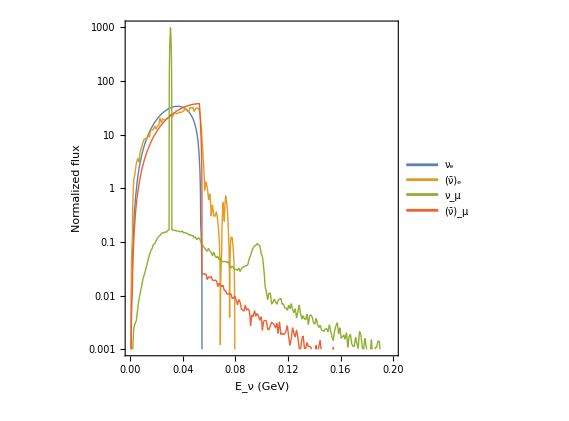

```mathematica
LogPlot[{snsFlux1DnuE[Enu],snsFlux1DnuEbar[Enu],snsFlux1DnuMu[Enu],snsFlux1DnuMubar[Enu]},{Enu,.0005,.2},PlotRange->{10^-3,10^3},
PlotLegends->Legend[{"ν_e","(ν̄)_e","ν_μ","(ν̄)_μ"}],FrameLabel->{"E_ν (GeV)","Normalized flux"}]
```

Create flux objects just for energy

```mathematica
snsFluxEνE={"Spectrum",snsFlux1DnuE,.5MeV,600MeV,"νe"};
snsFluxEνM={"Spectrum",snsFlux1DnuMu,.5MeV,600MeV,"νμ"};
snsFluxEνMb={"Spectrum",snsFlux1DnuMubar,.5MeV,600MeV,"νμb"};
cohSNSspectra={snsFluxEνE,snsFluxEνM,snsFluxEνMb};
```

## Standard CEvNS

### Kinematics

Elastic:

```mathematica
TMIN[TT_?NumericQ,mi_?NumericQ,mT_?NumericQ]:=If[TT<2mi,
(TT/2-mi)(1-√(1+(2TT(mi+mT)^2)/(mT(2mi-TT)^2))),
(TT/2-mi)(1+√(1+(2TT(mi+mT)^2)/(mT(2mi-TT)^2)))];
```

```mathematica
TMAX[Ti_?NumericQ,mi_?NumericQ,mT_?NumericQ]:=(Ti^2+2mi Ti)/(Ti+(mi+mT)^2/(2 mT));
```

```mathematica
EnuMin[q_,ω_]:=(q+ω)/2
```

### Cross section

#### Define differential cross section

These cross section functions are designed to have the same arguments so that they can be used interchangeably with the rate functions below.

Standard cross section with single form factor

```mathematica
dσdEr[Er_,Eν_,iso_,FFtype_:"Klein"]:=(Gf^2 iso[mT])/(4π)(1-(iso[mT] Er)/(2 Eν^2)-Er/Eν)(iso[Z] Qwp+(iso[A]-iso[Z]) Qwn)^2 FF[√(2iso[mT]Er),iso,FFtype]^2 UnitStep[TMAX[Eν,0,iso[mT]]-Er]
```

```mathematica
dσWdEr[Er_,Eν_,iso_,νf_,FFtype_:"NA"]:=(Gf^2 iso[mT])/(4π)(1-(iso[mT] Er)/(2 Eν^2)-Er/Eν)FfermiW[√(2iso[mT]Er),iso,νf]UnitStep[TMAX[Eν,0,iso[mT]]-Er]
```

Define another cross section with flavor dependent charges and independent form factors:

```mathematica
dσIFdEr[Er_,Eν_,iso_,νf_,FFtype_:"Klein"]:=(Gf^2 iso[mT])/(4π)(1-(iso[mT] Er)/(2 Eν^2)-Er/Eν)(iso[Z] QVp[νf] FF[√(2iso[mT]Er),iso,FFtype,"proton"]+(iso[A]-iso[Z]) QVn FF[√(2iso[mT]Er),iso,FFtype,"neutron"])^2 UnitStep[TMAX[Eν,0,iso[mT]]-Er]
```

#### Total cross section

```mathematica
σ[Enu_,iso_,FFtype_:"Helm"]:=NIntegrate[dσdEr[Er,Enu,iso,FFtype],{Er,0,TMAX[Enu,0,iso[mT]]},PrecisionGoal->3]
σf[Enu_,iso_,νf_,FFtype_:"Helm"]:=NIntegrate[dσfdEr[Er,Enu,iso,νf,FFtype],{Er,0,TMAX[Enu,0,iso[mT]]}]
```

## Full cross section

This is based on the definitions from arXiv:2007.08529:

### Form factors

Weak (SI):

Put SI form factors in terms of proton/neutron basis (using Hoferichter def)

```mathematica
ℱMn[Q_,isotope_]:=√((4π)/(2isotope[J]+1)(isotope[WM00]+isotope[WM11]-isotope[WM01]-isotope[WM10])/.q->Q);
ℱMp[Q_,isotope_]:=√((4π)/(2isotope[J]+1)(isotope[WM00]+isotope[WM11]+isotope[WM01]+isotope[WM10])/.q->Q);
ℱΦn[Q_,isotope_]:=√((4π)/(2isotope[J]+1)(isotope[WΦ00]+isotope[WΦ11]-isotope[WΦ01]-isotope[WΦ10])/.q->Q);
ℱΦp[Q_,isotope_]:=√((4π)/(2isotope[J]+1)(isotope[WΦ00]+isotope[WΦ11]+isotope[WΦ01]+isotope[WΦ10])/.q->Q);
```

Slightly changed definition for consistency

```mathematica
Fw[q_,isotope_,νf_]:=(((QVp[νf](1-r2Ep/6 q^2-1/(8 mn^2)q^2)-QVn(r2En+r2EsN)/6 q^2)ℱMp[q,isotope]+(QVn(1-(r2Ep+r2EsN)/6 q^2-1/(8 mn^2)q^2)-QVp[νf] r2En/6 q^2)ℱMn[q,isotope])+(QVp[νf](1+2κp)+2QVn(κn+κsN))/(4 mn^2)q^2 ℱΦp[q,isotope]+(QVp[νf](1+2κp+2κsN)+2QVp[νf] κn)/(4 mn^2)q^2 ℱΦn[q,isotope])^2;
```

SD:

```mathematica
Iσ1[ρ_,Q_]=1/(512 kF^3 Q^3)(8kF Q(48(kF^2+mπ^2)^2+32(kF^2-3 mπ^2)Q^2-3 Q^4)+768 mπ^3 Q^3 ArcCot[(mπ^2+Q^2/4-kF^2)/(2mπ kF)]+3(16(kF^2+mπ^2)^2-8(kF^2-5 mπ^2)Q^2+Q^4)(4(kF^2+mπ^2)-Q^2)Log[(mπ^2+(kF-Q/2)^2)/(mπ^2+(kF+Q/2)^2)])/.kF->((3 π^2 ρ)/2)^(1/3);
Iσ2[ρ_,Q_]=1/(16 kF^3 Q)(8kF(2 kF^2-3 mπ^2)Q+24 mπ^3 Q ArcCot[(mπ^2+Q^2/4-kF^2)/(2mπ kF)]+3 mπ^2(4 kF^2-Q^2+4 mπ^2)Log[(mπ^2+(kF-Q/2)^2)/(mπ^2+(kF+Q/2)^2)])/.kF->((3 π^2 ρ)/2)^(1/3);
Ic6[ρ_,Q_]=-9/(128 kF^3 Q)((32 kF^3 Q+32kF mπ^2 Q+8 kF Q^3)+(16(kF^2+mπ^2)^2+8(mπ^2-kF^2)Q^2+Q^4)Log[(4 mπ^2+(2kF-Q)^2)/(4 mπ^2+(2kF+Q)^2)])/.kF->((3 π^2 ρ)/2)^(1/3);
Λχ=700MeV;
cD=-3;(*in principle should be set from hamiltonian used in shell model calc*)

δa[q_]=-ρD/Fπ^2(c4/3(3Iσ2[ρD,q]-Iσ1[ρD,q])-1/3(c3-1/(4 mn))Iσ1[ρD,q]-c6/12 Ic6[ρD,q]-cD/(4gA Λχ));

δ[q_]=-(q^2 rA2)/6+δa[q]//Simplify;
```

The δ  capture the combined effect of the pseudoscalar form factor, radius corrections, and two - body currents

```mathematica
S00[Q_,isotope_]:=isotope[WΣ00]/.q->Q;
S11[Q_,isotope_]:=(1+δ[q])^2 isotope[WΣ11]/.q->Q;
S01[Q_,isotope_]:=2(1+δ[q])isotope[WΣ01]/.q->Q;
```

Eq. 67

```mathematica
FA[q_,isotope_]:=(8π)/(2isotope[J]+1)(gAs^2 S00[q,isotope]-gA gAs S01[q,isotope]+gA^2 S11[q,isotope])
```

### Cross section

Differential:
(FFtype is not used, but preserved for compatibility)

```mathematica
dσFulldEr//Clear;
dσFulldEr[Er_,Eν_,isotope_,νf_,FFtype_:"NA"]:=(Gf^2 isotope[mT])/(4π)((1-(isotope[mT] Er)/(2 Eν^2)-Er/Eν)Fw[√(2 isotope[mT] Er),isotope,νf]+(1+(isotope[mT] Er)/(2 Eν^2)-Er/Eν)FA[√(2 isotope[mT] Er),isotope])UnitStep[TMAX[Eν,0,isotope[mT]]-Er];
```

Total cross section:

```mathematica
σFull//Clear;
σFull[Enu_?NumericQ,iso_]:=NIntegrate[dσFulldEr[Er,Enu,iso],{Er,1eV,TMAX[Enu,0,iso[mT]]},PrecisionGoal->3,WorkingPrecision->16]
```

#### Just SI term

Defining cross section with M form factor only, for comparison purposes:

```mathematica
Fw[.01,targetCsI[[1]],"νe"]
```

5039.4

```mathematica
FM[.01,targetCsI[[1]],"νe"]
```

5039.58

```mathematica
FM//Clear;
FM[q_,isotope_,νf_]:=((QVp[νf](1-r2Ep/6 q^2-1/(8 mn^2)q^2)-QVn(r2En+r2EsN)/6 q^2)ℱMp[q,isotope]+(QVn(1-(r2Ep+r2EsN)/6 q^2-1/(8 mn^2)q^2)-QVp[νf] r2En/6 q^2)ℱMn[q,isotope])^2;
dσMdEr//Clear;
dσMdEr[Er_,Eν_,isotope_,νf_,FFtype_:"NA"]:=(Gf^2 isotope[mT])/(4π)((1-(isotope[mT] Er)/(2 Eν^2)-Er/Eν)FM[√(2 isotope[mT] Er),isotope,νf]+(1+(isotope[mT] Er)/(2 Eν^2)-Er/Eν)FA[√(2 isotope[mT] Er),isotope])UnitStep[TMAX[Eν,0,isotope[mT]]-Er];
```

## Flux averaged cross sections

### Definition

```mathematica
σAvg[target_,spectra_,dσdE_,FFtype_:"NA"]:=Module[{minMT,Integrand},
Integrand[er_?NumericQ,Eν_?NumericQ]=Sum[spectra[[j,2]][Eν]target[[i]][f]dσdE[er,Eν,target[[i]],spectra[[j,5]],FFtype],{i,1,Length[target]},{j,1,Length[spectra]}];
minMT=Min[Table[target[[i]][mT],{i,1,Length[target]}]];1/(Sum[target[[i]][f],{i,1,Length[target]}]Length[spectra])NIntegrate[Integrand[er,Eν],{er,1eV,TMAX[Max[spectra[[All,4]]],0,minMT]},{Eν,Min[TMIN[er,0,minMT],Max[spectra[[All,4]]]],Max[spectra[[All,4]]]},Method->{Automatic,"SymbolicProcessing"->0},PrecisionGoal->3]]
```

### Cesium-Iodide

```mathematica
σAvgCsIcohPredicted=Around[189,6] 10^-40
```

1.890.0610^-38

```mathematica
{{σAvgCsIKN,σAvgCsIKNalt},{σAvgCsIFull,σAvgCsIFullAlt},{σAvgCsISHF,σAvgCsISHFAlt},{σAvgCsIM,σAvgCsIMAlt}}=ParallelTable[σAvg[target,cohSNSspectra,dσdE,"Klein"]/Centimeter^2,{dσdE,{dσIFdEr,dσFulldEr,dσWdEr,dσMdEr}},{target,{targetCsI,targetCsIalt}}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Uncertainty quantification:

From the normalisation constant:

```mathematica
normUnσCsI=QWun[targetCsI[[1]],"νe"]/QW[targetCsI[[1]],"νe"]
```

1.00000.0025

And from the form factors:

```mathematica
σAvgCsIKNresult=Around[(σAvgCsIKN+σAvgCsIKNalt)/2,(σAvgCsIKN-σAvgCsIKNalt)/2]normUnσCsI;
σAvgCsIFullresult=Around[(σAvgCsIFull+σAvgCsIFullAlt)/2,(σAvgCsIFull-σAvgCsIFullAlt)/2]normUnσCsI;
σAvgCsISHFresult=Around[(σAvgCsISHF+σAvgCsISHFAlt)/2,(σAvgCsISHF-σAvgCsISHFAlt)/2]normUnσCsI;
σAvgCsIMresult=Around[(σAvgCsIM+σAvgCsIMAlt)/2,(σAvgCsIM-σAvgCsIMAlt)/2]normUnσCsI;
```

```mathematica
σAvgCsIFullresult
```

1.8630.00510^-38

```mathematica
σAvgCsIMresult
```

1.8640.00510^-38

```mathematica
σAvgCsIMAlt
```

1.86578×10^-38

```mathematica
CsIσPlot=Show[ListPlot[{{.5,σAvgCsIcohPredicted 10^39}},PlotStyle->{Black,Thick},
AspectRatio->.5,FrameLabel->{None,"⟨σ⟩_Φ (10^-39cm^2)"},PlotRange->{{0,3},{13.8,19.99}},FrameTicks->{None,Automatic},
Prolog->{
Inset[Style["COHERENT",15,Black],Scaled[{.15,.1}]],
Inset[Style["Charge",16,MyBlue],Scaled[{.4,.1}]],
Inset[Style["SHF",16,MyRed],Scaled[{.6,.1}]],
Inset[Style["Shell model",16,MyGreen],Scaled[{.825,.1}]],
Inset[Style["Current exp.",Italic,14,Black],Scaled[{.15,.5}]],
Inset[Style["Future exp.",Italic,14,Purple],Scaled[{.85,.36}]],
Inset[Style["Cesium-Iodide",18,Black,Bold,FontFamily->"Times"],Scaled[{.8,.92}]]}],
ListPlot[{{1.2,σAvgCsIKNresult 10^39}},PlotStyle->{MyBlue,Thick}],
ListPlot[{{1.8,σAvgCsISHFresult 10^39}},PlotStyle->{MyRed,Thick}],
ListPlot[{{2.5,σAvgCsIFullresult 10^39}},PlotStyle->{MyGreen,Thick}],
Plot[{14.0,19.5,16.5,16.5+16.5*.05,16.5-16.5*.05},{x,0,4},Filling->{1->{2},4->{5}},FillingStyle->{Opacity[.1,Gray],Directive[HatchFilling[π/4,4,8],Opacity[.1,Purple]]},PlotStyle->{None,None,{Black,Dashed},None,None}]]
```

-Graphics-

```mathematica
Export["figures/fig_CsI_cs.pdf",CsIσPlot]
```

figures/fig_CsI_cs.pdf

#### Ratio plot

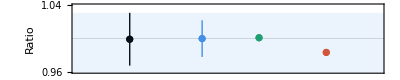

```mathematica
CsIσPlotRatio=Show[ListPlot[{{1.5,σAvgCsIKNresult/σAvgCsIKNresult["Value"] }},PlotStyle->{MyBlue,Thick,10},
AspectRatio->.2,FrameLabel->{None,"Ratio"},PlotRange->{{.3,3.2},{0.96,1.04}},
FrameTicks->{{{{0.96,0.96},{0.98,None},1,{1.02,None},1.04},Automatic},None},
GridLines->{None,{1}}],
ListPlot[{{2.7,σAvgCsIFullresult/σAvgCsIKNresult["Value"]}},PlotStyle->{MyRed,Thick}],
ListPlot[{{.8,σAvgCsIcohPredicted/σAvgCsIKNresult["Value"]}},PlotStyle->{Black,Thick}],
ListPlot[{{2.05,σAvgCsISHFresult/σAvgCsIKNresult["Value"]}},PlotStyle->{MyGreen,Thick}],
Plot[{(14.0 10^-39)/σAvgCsIKNresult["Value"],(19.5 10^-39)/σAvgCsIKNresult["Value"],(16.5 10^-39)/σAvgCsIKNresult["Value"]},{x,0,4},Filling->{1->{2}},FillingStyle->{Opacity[.1,MyBlue]},PlotStyle->{None,None,{MyBlue,Dashed},{Black,Dashed}}]]
```

```mathematica
ResourceFunction["PlotGrid"][{{CsIσPlot},{CsIσPlotRatio}},ItemSize->{Automatic,{4}},AspectRatio->.6]
```

-Graphics-

#### Affect on measured cross section

How the cross section affects the interpreted measured value:

```mathematica
With[{NCsI=(14.56Kilogram)/(.5Cs133[mT]+.5I127[mT]),Φ=3(3.198 10^23 Around[0.0848,.00848])/(4π (19.3 100)^2),Nobs=Around[306,20],Nexp=341,avgEff=avgEfficiency},
sigmaAvgMeasuredCOHERENT=Nobs/(avgEff NCsI Φ);
sigmaAvgPredictedCOHERENT=Nexp/(avgEff NCsI Φ);]
```

```mathematica
sigmaAvgPredictedCOHERENT=Around[189,6] 10^-40
```

1.890.0610^-38

```mathematica
With[{NCsI=(14.56Kilogram)/(.5Cs133[mT]+.5I127[mT]),Φ=3(3.198 10^23 0.0848)/(4π (19.3 100)^2),Nobs=Around[306,20],
NexpKN=KNtotRateCoherentCsI,NexpFull=fullTotRateCoherentCsI,avgEffKN=avgEfficiencyKN,avgEffFull=avgEfficiencyFull},

sigmaAvgMeasuredKN=Nobs/(avgEffKN NCsI Φ);

sigmaAvgMeasuredFull=Nobs/(avgEffFull NCsI Φ);
]
```

### Argon

For argon predicted: 1.8±.04 10^-39, measured 2.3±0.7

```mathematica
σAvgArCohPredicted=Around[1.8,.04] 10^-39;
σAvgArCohMeasured=Around[2.3,.7] 10^-39;
```

```mathematica
{{σAvgArKN,σAvgArKNalt},{σAvgArFull,σAvgArFullAlt},{σAvgArSHF,σAvgArSHFalt},{σAvgArM,σAvgArMalt}}=ParallelTable[σAvg[target,cohSNSspectra,dσdE,"Klein"]/Centimeter^2,{dσdE,{dσIFdEr,dσFulldEr,dσWdEr,dσMdEr}},{target,{targetAr,targetArAlt}}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Uncertainty quantification:

From the form factors:

```mathematica
normUnσAr=QWun[targetAr[[1]],"νe"]/QW[targetAr[[1]],"νe"]
```

1.00000.0029

```mathematica
σAvgArKNresult=Around[(σAvgArKN+σAvgArKNalt)/2,(σAvgArKN-σAvgArKNalt)/2]normUnσAr;
σAvgArFullresult=Around[(σAvgArFull+σAvgArFullAlt)/2,(σAvgArFull-σAvgArFullAlt)/2]normUnσAr;
σAvgArSHFresult=Around[(σAvgArSHF+σAvgArSHFalt)/2,(σAvgArSHF-σAvgArSHFalt)/2]normUnσAr;
σAvgArMresult=Around[(σAvgArM+σAvgArMalt)/2,(σAvgArM-σAvgArMalt)/2]normUnσAr;
```

```mathematica
ArσPlot=Show[ListPlot[{{.5, σAvgArCohPredicted 10^40}},PlotStyle->{{Black,Thick}},
AspectRatio->.5,FrameLabel->{None,"⟨σ⟩_Φ (10^-40cm^2)"},PlotRange->{{0,3},{15.5,23.5}},FrameTicks->{None,Automatic},
Prolog->{
Inset[Style["COHERENT",15,Black],Scaled[{.17,.11}]],
Inset[Style["Charge",16,MyBlue],Scaled[{.4,.11}]],
Inset[Style["SHF",16,MyRed],Scaled[{.6,.11}]],
Inset[Style["Shell model",16,MyGreen],Scaled[{.825,.11}]],
Inset[Style["Current exp.",Italic,14,Black],Scaled[{.145,.65}]],
Inset[Style["Future exp.",Italic,14,Purple],Scaled[{.14,.86}]],
Inset[Style["Argon",18,Black,Bold,FontFamily->"Times"],Scaled[{.88,.86}]]}],
ListPlot[{{1.2,σAvgArKNresult 10^40}},PlotStyle->{MyBlue,Thick}],
ListPlot[{{1.8,σAvgArSHFresult 10^40}},PlotStyle->{MyRed,Thick}],
ListPlot[{{2.5,σAvgArFullresult 10^40}},PlotStyle->{MyGreen,Thick}],
Plot[{16,30,23,23+.05 23,23-.05 23},{x,0,4},Filling->{1->{2},4->{5}},FillingStyle->{Opacity[.1,Gray],Directive[HatchFilling[π/4,4,8],Opacity[.1,Purple]]},PlotStyle->{None,None,{Black,Dashed},None,None}]]
```

-Graphics-

```mathematica
Export["figures/fig_Ar_cs.pdf",ArσPlot];
```

### Germanium

```mathematica
{{σAvgGeKN,σAvgGeKNalt},{σAvgGeFull,σAvgGeFullAlt},{σAvgGeSHF,σAvgGeSHFalt},{σAvgGeM,σAvgGeMalt}}=ParallelTable[σAvg[target,cohSNSspectra,dσdE,"Klein"]/Centimeter^2,{dσdE,{dσIFdEr,dσFulldEr,dσWdEr,dσMdEr}},{target,{targetGe,targetGeAlt}}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Uncertainty quantification:

```mathematica
normUnσGe=QWun[targetGe[[1]],"νe"]/QW[targetGe[[1]],"νe"]
```

1.00000.0030

From the form factors:

```mathematica
σAvgGeKNresult=Around[(σAvgGeKN+σAvgGeKNalt)/2,(σAvgGeKN-σAvgGeKNalt)/2]normUnσGe;
σAvgGeFullresult=Around[(σAvgGeFull+σAvgGeFullAlt)/2,(σAvgGeFull-σAvgGeFullAlt)/2]normUnσGe;
σAvgGeSHFresult=Around[(σAvgGeSHF+σAvgGeSHFalt)/2,(σAvgGeSHF-σAvgGeSHFalt)/2]normUnσGe;
σAvgGeMresult=Around[(σAvgGeM+σAvgGeMalt)/2,(σAvgGeM-σAvgGeMalt)/2]normUnσGe;
```

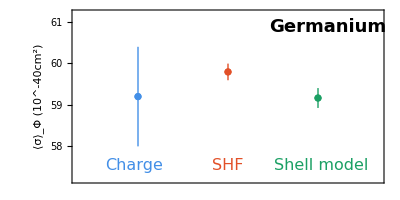

```mathematica
GeσPlot=Show[ListPlot[{{.6,σAvgGeKNresult 10^40}},PlotStyle->{MyBlue,Thick,10},
AspectRatio->.5,FrameLabel->{None,"⟨σ⟩_Φ (10^-40cm^2)"},PlotRange->{{0,3},{57.2,61.2}},FrameTicks->{None,Automatic},
Prolog->{
Inset[Style["Charge",16,MyBlue],Scaled[{.2,.1}]],
Inset[Style["SHF",16,MyRed],Scaled[{.5,.1}]],
Inset[Style["Shell model",16,MyGreen],Scaled[{.8,.1}]],
Inset[Style["Germanium",18,FontFamily->"Times",Black,Bold],Scaled[{.82,.9}]]}],
ListPlot[{{1.5,σAvgGeSHFresult 10^40}},PlotStyle->{MyRed,Thick}],
ListPlot[{{2.4,σAvgGeFullresult 10^40}},PlotStyle->{MyGreen,Thick}]]
```

```mathematica
Export["figures/fig_Ge_cs.pdf",GeσPlot]
```

figures/fig_Ge_cs.pdf

## Differential rate definition

Define the experimental targets, CsI and argon

```mathematica
dRcevnsSdE[Er_?NumericQ,targets_,spec_,Eνmin_,Eνmax_,νf_,dσdE_:dσdEr]:=1/(Plus@@(#[mT]&/@targets)) Sum[isotope[f]NIntegrate[ spec[Enu] dσdE[Er,Enu,isotope,νf],{Enu,Min[Max[Eνmin,TMIN[Er,0,isotope[mT]]],Eνmax],Eνmax},PrecisionGoal->3]
,{isotope,targets}]
dRcevnsLdE[Er_?NumericQ,targets_,Eν_,νf_,dσdE_:dσdEr]:=1/(Plus@@(#[mT]&/@targets))  Sum[isotope[f] dσdE[Er,Eν,isotope,νf]HeavisideTheta[Eν-TMIN[Er,0,isotope[mT]]],{isotope,targets}]

dRcevnsdE[Er_?NumericQ,target_,spectra_,flux_?NumericQ,dσdE_:dσdEr]:=
flux Sum[
Switch[spec[[1]],
"Line",dRcevnsLdE[Er,target,spec[[2]],dσdE],
"Spectrum",dRcevnsSdE[Er,target,spec[[2]],spec[[3]],spec[[4]],dσdE]]
,{spec,spectra}];
dRcevnsdE[Er_?NumericQ,target_,spectra_,fluxes_?ListQ,dσdE_:dσdEr]:=
 Sum[fluxes[[speci]]
Switch[spectra[[speci,1]],
"Line",dRcevnsLdE[Er,target,spectra[[speci,2]],spectra[[speci,-1]],dσdE],
"Spectrum",dRcevnsSdE[Er,target,spectra[[speci,2]],spectra[[speci,3]],spectra[[speci,4]],spectra[[speci,5]],dσdE]]
,{speci,1,Length[spectra]}];
```

With timing:

```mathematica
dRcevnsSdEdT[Er_?NumericQ,T_?NumericQ,targets_,spec_,Eνmin_,Eνmax_,dσdE_:dσdEr]:=1/(Plus@@(#[mT]&/@targets)) Sum[isotope[f]NIntegrate[ spec[T,Enu] dσdE[Er,Enu,isotope],{Enu,Min[Max[Eνmin,TMIN[Er,0,isotope[mT]]],Eνmax],Eνmax},PrecisionGoal->3]
,{isotope,targets}]
(*Line def incomplete, not used*)
dRcevnsLdEdT[Er_?NumericQ,T_?NumericQ,targets_,spec_,Eν_,dσdE_:dσdEr]:=1/(Plus@@(#[mT]&/@targets))  spec[T,Eν]Sum[isotope[f] dσdE[Er,Eν,isotope]HeavisideTheta[Eν-TMIN[Er,0,isotope[mT]]],{isotope,targets}]

dRcevnsdEdT[Er_?NumericQ,T_?NumericQ,target_,spectra_,flux_?NumericQ,dσdE_:dσdEr]:=
flux Sum[
Switch[spec[[1]],
"Line",dRcevnsLdEdT[Er,T,target,spec[[2]],dσdE],
"Spectrum",dRcevnsSdEdT[Er,T,target,spec[[2]],spec[[3]],spec[[4]],dσdE]]
,{spec,spectra}]
```

## Comparison plots

### Comparing form factors

#### Spin-independent

Compare form factors:

```mathematica
FFplotI=Show[LogPlot[{
FwCharge[q,targetCsI[[2]],"νe","Klein"],
FfermiW[q,targetCsI[[2]],"νe"],
Fw[q,targetCsI[[2]],"νe"],
FwCharge[q,targetCsIalt[[2]],"νe","Klein"],
FfermiW[q,targetCsIalt[[2]],"νe"],
Fw[q,targetCsIalt[[2]],"νe"]},
{q,0,0.215},PlotRange->{1.1,1.1 QW[targetCsI[[2]],"νe"]^2},
PlotStyle->{MyBlue,MyRed,MyGreen,MyBlue,MyRed,MyGreen},
Filling->{1->{4},2->{5},3->{6}},AspectRatio->0.8,
FrameLabel->{None,"Form factor, Q_w^2F_w^2(q^2)"},
PlotLegends->Legend[{"Charge","SHF","Shell"},Position->{.82,.68},LegendMarkerSize->14]],
LogPlot[{10^4 HeavisideTheta[√(2 targetCsI[[2]][mT] 4.35keV)-q]+.001,10^4 HeavisideTheta[q-√(2 targetCsI[[2]][mT] TMAX[53MeV,0,targetCsI[[2]][mT]])]+.001},
{q,-.1,0.28},PlotStyle->{Gray,Gray},
PlotRange->{.1,10^5},Filling->{1->.001,2->.001}],Epilog->{Inset[Style["Iodine-127",16,Black,FontFamily->"Times",Bold],Scaled[{.81,.92}]],
Inset[Style["COHERENT \nCsI ROI",15,Black],Scaled[{.335,.24}]],
Arrow[{{√(2 targetCsI[[2]][mT] 4.35keV),1},{√(2 targetCsI[[2]][mT] TMAX[53MeV,0,targetCsI[[2]][mT]]),1}}],Arrow[{{√(2 targetCsI[[2]][mT] TMAX[53MeV,0,targetCsI[[2]][mT]]),1},{√(2 targetCsI[[2]][mT] 4.35keV),1}}]},
ImageSize->400];
ratioPlotI=Show[Plot[{
FfermiW[q,targetCsI[[2]],"νe"]/FwCharge[q,targetCsIalt[[2]],"νe","Klein"],
Fw[q,targetCsI[[2]],"νe"]/FwCharge[q,targetCsIalt[[2]],"νe","Klein"],
FfermiW[q,targetCsIalt[[2]],"νe"]/FwCharge[q,targetCsI[[2]],"νe","Klein"],
Fw[q,targetCsIalt[[2]],"νe"]/FwCharge[q,targetCsI[[2]],"νe","Klein"]
},
{q,0.001,0.215},PlotStyle->{MyRed,MyGreen,MyRed,MyGreen},
Filling->{1->{3},2->{4}},AspectRatio->0.2,GridLines->{None,{0.5,1,1.5}},
FrameTicks->{{{0.5,1,1.5},Automatic},Automatic},
FrameLabel->{"Momentum transfer, q (GeV)","Ratio"},
PlotRange->{.3,1.7}],LogPlot[{10^4 HeavisideTheta[√(2 targetCsI[[2]][mT] 4.35keV)-q]+.001,10^4 HeavisideTheta[q-√(2 targetCsI[[2]][mT] TMAX[53MeV,0,targetCsI[[2]][mT]])]+.001},
{q,-.1,0.28},PlotStyle->{Gray,Gray},Filling->{1->.001,2->.001}]];
```

```mathematica
SIFFplotI=ResourceFunction["PlotGrid"][{{FFplotI},{ratioPlotI}},ItemSize->{Automatic,{3.}},AspectRatio->1]//Show[#,ImageSize->320]&
```

-Graphics-

```mathematica
FFplotAr=Show[LogPlot[{
FwCharge[q,targetAr[[1]],"νe","Klein"],
FfermiW[q,targetAr[[1]],"νe"],
Fw[q,targetAr[[1]],"νe"],
FwCharge[q,targetArAlt[[1]],"νe","Klein"],
FfermiW[q,targetArAlt[[1]],"νe"],
Fw[q,targetArAlt[[1]],"νe"]},
{q,0.001,0.21},PlotRange->{1.1,1.5 QW[targetAr[[1]],"νe"]^2},
PlotStyle->{MyBlue,MyRed,MyGreen,MyBlue,MyRed,MyGreen},
Filling->{1->{4},2->{5},3->{6}},AspectRatio->0.8,
FrameLabel->{None,"Form factor, Q_w^2F_w^2(q^2)"},
PlotLegends->Legend[{"Charge","SHF","Shell"},Position->{.85,.7},LegendMarkerSize->14]],
LogPlot[{10^5 HeavisideTheta[√(2 targetAr[[1]][mT]5 keV)-q]+.001,10^5 HeavisideTheta[q-√(2 targetAr[[1]][mT] TMAX[53MeV,0,targetAr[[1]][mT]])]+.001},
{q,-.1,0.22},PlotStyle->{Gray,Gray},
PlotRange->{.1,10^5},Filling->{1->.001,2->.001}],Epilog->{Inset[Style["Argon-40",16,Black,FontFamily->"Times",Bold],Scaled[{.85,.93}]],
Inset[Style["COHERENT \nAr ROI",15,Black],Scaled[{.31,.32}]],
Arrow[{{√(2 targetAr[[1]][mT] 5keV),1.2},{√(2 targetAr[[1]][mT] TMAX[53MeV,0,targetAr[[1]][mT]]),1.2}}],Arrow[{{√(2targetAr[[1]][mT] TMAX[53MeV,0,targetAr[[1]][mT]]),1.2},{√(2 targetAr[[1]][mT] 4.7keV),1.2}}]},
ImageSize->400];
ratioPlotAr=Show[Plot[{
FfermiW[q,targetAr[[1]],"νe"]/FwCharge[q,targetArAlt[[1]],"νe","Klein"],
Fw[q,targetAr[[1]],"νe"]/FwCharge[q,targetArAlt[[1]],"νe","Klein"],
FfermiW[q,targetArAlt[[1]],"νe"]/FwCharge[q,targetAr[[1]],"νe","Klein"],
Fw[q,targetArAlt[[1]],"νe"]/FwCharge[q,targetAr[[1]],"νe","Klein"]
},
{q,0.001,0.21},PlotStyle->{MyRed,MyGreen,MyRed,MyGreen},
Filling->{1->{3},2->{4}},AspectRatio->0.2,GridLines->{None,{0.9,1,1.1}},
FrameTicks->{{{0.9,1,1.1},Automatic},Automatic},
FrameLabel->{"Momentum transfer, q (GeV)","Ratio"},
PlotRange->{.82,1.2}],
LogPlot[{10^4 HeavisideTheta[√(2 targetAr[[1]][mT] 5keV)-q]+.001,10^4 HeavisideTheta[q-√(2 targetAr[[1]][mT] TMAX[53MeV,0,targetAr[[1]][mT]])]+.001},
{q,-.1,0.22},PlotStyle->{Gray,Gray},Filling->{1->.001,2->.001}]];
```

```mathematica
SIFFplotAr=ResourceFunction["PlotGrid"][{{FFplotAr},{ratioPlotAr}},ItemSize->{Automatic,{3}},AspectRatio->1]//Show[#,ImageSize->320]&
```

-Graphics-

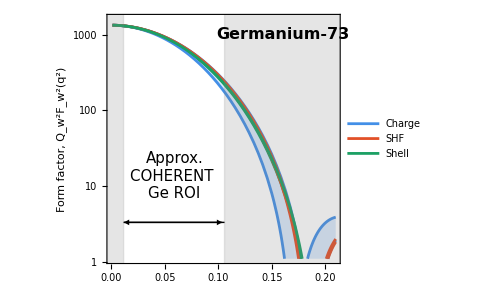
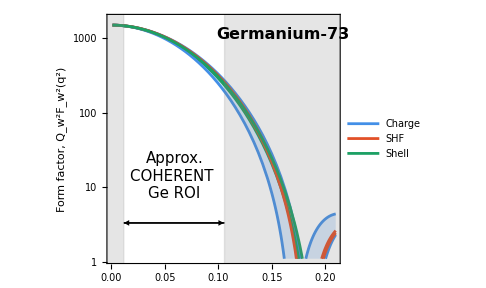
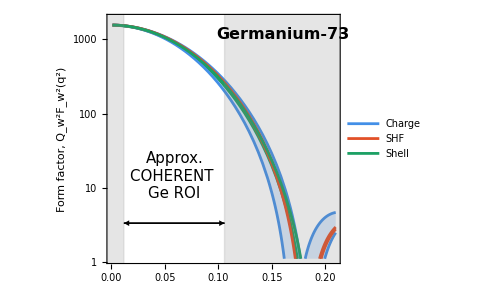
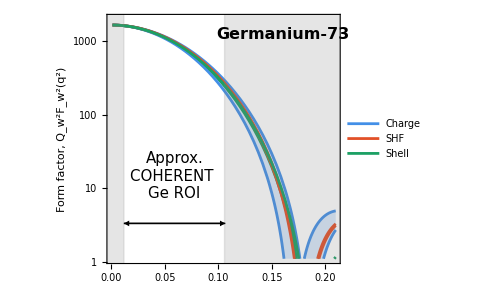
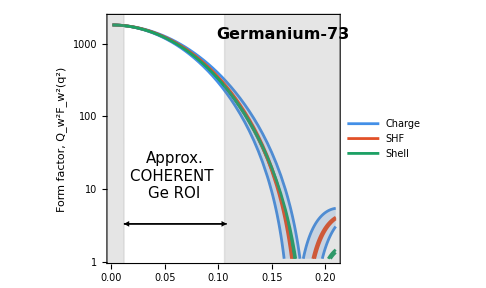

```mathematica
Table[Show[LogPlot[{
FwCharge[q,targetGe[[i]],"νe","Klein"],
FfermiW[q,targetGe[[i]],"νe"],
Fw[q,targetGe[[i]],"νe"],
FwCharge[q,targetGeAlt[[i]],"νe","Klein"],
FfermiW[q,targetGeAlt[[i]],"νe"],
Fw[q,targetGeAlt[[i]],"νe"]},
{q,0.001,0.21},PlotRange->{1.1,1.2 QW[targetGe[[i]],"νe"]^2},
PlotStyle->{MyBlue,MyRed,MyGreen,MyBlue,MyRed,MyGreen},
Filling->{1->{4},2->{5},3->{6}},AspectRatio->0.8,
FrameLabel->{None,"Form factor, Q_w^2F_w^2(q^2)"},
PlotLegends->Legend[{"Charge","SHF","Shell"},Position->{.82,.68},LegendMarkerSize->14]],
LogPlot[{10^5 HeavisideTheta[√(2 targetGe[[i]][mT]1 keV)-q]+.001,10^5 HeavisideTheta[q-√(2 targetGe[[i]][mT] TMAX[53MeV,0,targetGe[[i]][mT]])]+.001},
{q,-.1,0.24},PlotStyle->{Gray,Gray},
PlotRange->{.1,10^8},Filling->{1->.001,2->.001}],Epilog->{Inset[Style["Germanium-73",16,Black,FontFamily->"Times",Bold],Scaled[{.755,.92}]],
Inset[Style["Approx.\nCOHERENT \nGe ROI",15,Black],Scaled[{.29,.35}]],
Arrow[{{√(2 targetGe[[i]][mT] 1keV),1.2},{√(2 targetGe[[i]][mT] TMAX[53MeV,0,targetGe[[3]][mT]]),1.2}}],Arrow[{{√(2targetGe[[i]][mT] TMAX[53MeV,0,targetGe[[i]][mT]]),1.2},{√(2 targetGe[[3]][mT] 1keV),1.2}}]},
ImageSize->360],{i,1,5}]
```

```mathematica
FFplotGe=Show[LogPlot[{
FwCharge[q,targetGe[[3]],"νe","Klein"],
FfermiW[q,targetGe[[3]],"νe"],
Fw[q,targetGe[[3]],"νe"],
FwCharge[q,targetGeAlt[[3]],"νe","Klein"],
FfermiW[q,targetGeAlt[[3]],"νe"],
Fw[q,targetGeAlt[[3]],"νe"]},
{q,0.001,0.21},PlotRange->{1.1,1.2 QW[targetGe[[3]],"νe"]^2},
PlotStyle->{MyBlue,MyRed,MyGreen,MyBlue,MyRed,MyGreen},
Filling->{1->{4},2->{5},3->{6}},AspectRatio->0.8,
FrameLabel->{None,"Form factor, Q_w^2F_w^2(q^2)"},
PlotLegends->Legend[{"Charge","SHF","Shell"},Position->{.82,.68},LegendMarkerSize->14]],
LogPlot[{10^5 HeavisideTheta[√(2 targetGe[[3]][mT]1 keV)-q]+.001,10^5 HeavisideTheta[q-√(2 targetGe[[3]][mT] TMAX[53MeV,0,targetGe[[3]][mT]])]+.001},
{q,-.1,0.24},PlotStyle->{Gray,Gray},
PlotRange->{.1,10^8},Filling->{1->.001,2->.001}],Epilog->{Inset[Style["Germanium-73",16,Black,FontFamily->"Times",Bold],Scaled[{.755,.92}]],
Inset[Style["Approx.\nCOHERENT \nGe ROI",15,Black],Scaled[{.29,.35}]],
Arrow[{{√(2 targetGe[[3]][mT] 1keV),1.2},{√(2 targetGe[[3]][mT] TMAX[53MeV,0,targetGe[[3]][mT]]),1.2}}],Arrow[{{√(2targetGe[[3]][mT] TMAX[53MeV,0,targetGe[[3]][mT]]),1.2},{√(2 targetGe[[3]][mT] 1keV),1.2}}]},
ImageSize->360];
ratioPlotGe=Show[Plot[{
FfermiW[q,targetGe[[3]],"νe"]/FwCharge[q,targetGeAlt[[3]],"νe","Klein"],
Fw[q,targetGe[[3]],"νe"]/FwCharge[q,targetGeAlt[[3]],"νe","Klein"],
FfermiW[q,targetGeAlt[[3]],"νe"]/FwCharge[q,targetGe[[3]],"νe","Klein"],
Fw[q,targetGeAlt[[3]],"νe"]/FwCharge[q,targetGe[[3]],"νe","Klein"]
},
{q,0.001,0.21},PlotStyle->{MyRed,MyGreen,MyRed,MyGreen},
Filling->{1->{3},2->{4}},AspectRatio->0.2,GridLines->{None,{0.8,1,1.2}},
FrameTicks->{{{0.8,1,1.2},Automatic},Automatic},
FrameLabel->{"Momentum transfer, q (GeV)","Ratio"},
PlotRange->{.72,1.3}],LogPlot[{10^4 HeavisideTheta[√(2 targetGe[[3]][mT] 1keV)-q]+.001,10^4 HeavisideTheta[q-√(2 targetGe[[3]][mT] TMAX[53MeV,0,targetGe[[3]][mT]])]+.001},
{q,-.1,0.28},PlotStyle->{Gray,Gray},Filling->{1->.001,2->.001}]];
```

```mathematica
SIFFplotGe=ResourceFunction["PlotGrid"][{{FFplotGe},{ratioPlotGe}},ItemSize->{Automatic,{3}},AspectRatio->1]//Show[#,ImageSize->320]&
```

-Graphics-

```mathematica
FFplotCs=Show[LogPlot[{
FwCharge[q,targetCsI[[1]],"νe","Klein"],
FfermiW[q,targetCsI[[1]],"νe"],
Fw[q,targetCsI[[1]],"νe"],
FwCharge[q,targetCsIalt[[1]],"νe","Klein"],
FfermiW[q,targetCsIalt[[1]],"νe"],
Fw[q,targetCsIalt[[1]],"νe"]},
{q,0,0.215},PlotRange->{1.1,1.1 QW[targetCsI[[1]],"νe"]^2},PlotStyle->{MyBlue,MyRed,MyGreen,MyBlue,MyRed,MyGreen},
Filling->{1->{4},2->{5},3->{6}},AspectRatio->0.8,
FrameLabel->{None,"Form factor, Q_w^2F_w^2(q^2)"},
PlotLegends->Legend[{"Charge","SHF","Shell"},Position->{.8,.68},LegendMarkerSize->14]],
LogPlot[{10^4 HeavisideTheta[√(2 targetCsI[[1]][mT] 4.35keV)-q]+.001,10^4 HeavisideTheta[q-√(2 targetCsI[[1]][mT] TMAX[53MeV,0,targetCsI[[1]][mT]])]+.001},
{q,-.1,0.28},PlotStyle->{Gray,Gray},
PlotRange->{.1,10^6},Filling->{1->.001,2->.001}],Epilog->{Inset[Style["Cesium-133",16,Black,FontFamily->"Times",Bold],Scaled[{.8,.93}]],
Inset[Style["COHERENT \nCsI ROI",15,Black],Scaled[{.335,.24}]],
Arrow[{{√(2 targetCsI[[1]][mT] 4.35keV),1},{√(2 targetCsI[[1]][mT] TMAX[53MeV,0,targetCsI[[1]][mT]]),1}}],Arrow[{{√(2 targetCsI[[1]][mT] TMAX[53MeV,0,targetCsI[[1]][mT]]),1},{√(2 targetCsI[[1]][mT] 4.35keV),1}}]},
ImageSize->360];
ratioPlotCs=Show[Plot[{
FfermiW[q,targetCsI[[1]],"νe"]/FwCharge[q,targetCsIalt[[1]],"νe","Klein"],
Fw[q,targetCsI[[1]],"νe"]/FwCharge[q,targetCsIalt[[1]],"νe","Klein"],
FfermiW[q,targetCsIalt[[1]],"νe"]/FwCharge[q,targetCsI[[1]],"νe","Klein"],
Fw[q,targetCsIalt[[1]],"νe"]/FwCharge[q,targetCsI[[1]],"νe","Klein"]
},
{q,0.001,0.215},PlotStyle->{MyRed,MyGreen,MyRed,MyGreen},
Filling->{1->{3},2->{4}},AspectRatio->0.2,GridLines->{None,{0.5,1,1.5}},
FrameTicks->{{{0.5,1,1.5},Automatic},Automatic},
FrameLabel->{"Momentum transfer, q (GeV)","Ratio"},
PlotRange->{.3,1.7}],LogPlot[{10^4 HeavisideTheta[√(2 targetCsI[[1]][mT] 4.35keV)-q]+.001,10^4 HeavisideTheta[q-√(2 targetCsI[[1]][mT] TMAX[53MeV,0,targetCsI[[1]][mT]])]+.001},
{q,-.1,0.28},PlotStyle->{Gray,Gray},Filling->{1->.001,2->.001}]];
```

```mathematica
SIFFplotCs=ResourceFunction["PlotGrid"][{{FFplotCs},{ratioPlotCs}},ItemSize->{Automatic,{3.}},AspectRatio->1]//Show[#,ImageSize->320]&
```

-Graphics-

```mathematica
Export["figures/fig_SIFF_Ar40.pdf",SIFFplotAr];
Export["figures/fig_SIFF_Ge73.pdf",SIFFplotGe];
Export["figures/fig_SIFF_I127.pdf",SIFFplotI];
Export["figures/fig_SIFF_Cs133.pdf",SIFFplotCs];
```

#### Spin-dependent

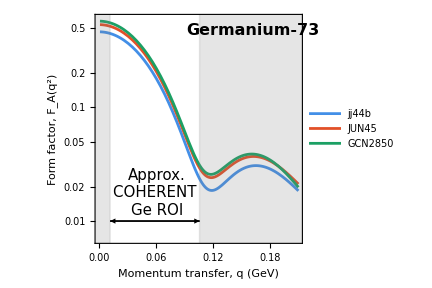
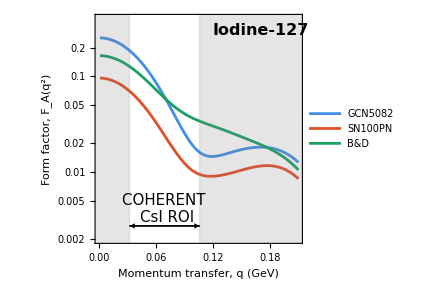
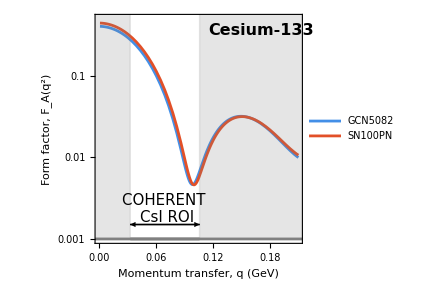

```mathematica
{With[{iso="Ge73"},
basePlotGe=LogPlot[{
FA[q,isotopesJJ44b[iso]],
FA[q,isotopesJUN45[iso]],
FA[q,isotopesDMFF[iso]]},
{q,0.001,0.21},
PlotRange->{7 10^-3,.6},AspectRatio->0.9,
PlotStyle->{MyBlue,MyRed,MyGreen},
FrameLabel->{"Momentum transfer, q (GeV)","Form factor, F_A(q^2)"},
PlotLegends->Legend[{"jj44b","JUN45","GCN2850"},Position->{.78,.72},LegendMarkerSize->14]];
SDFFplotGe=Show[basePlotGe,
LogPlot[{10^5 HeavisideTheta[√(2 isotopes[iso,mT] 1keV)-q]+.001,10^5 HeavisideTheta[q-√(2 isotopes[iso,mT] TMAX[53MeV,0,isotopes[iso,mT]])]+.001},
{q,-.1,0.23},PlotStyle->{Gray,Gray},
PlotRange->{10^-3,1.2(isotopes[iso,Z] Qwp+(isotopes[iso,A]-isotopes[iso,Z]) Qwn)^2},Filling->{1->.001,2->.001}],Epilog->{Inset[Style["Germanium-73",16,Black,FontFamily->"Times",Bold],Scaled[{.76,.93}]],
Inset[Style["Approx.\nCOHERENT \nGe ROI",15,Black],Scaled[{.3,.22}]],
Arrow[{{√(2 isotopes[iso,mT] 1keV),-4.6},{√(2 isotopes[iso,mT] TMAX[53MeV,0,isotopes[iso,mT]]),-4.6}}],Arrow[{{√(2 isotopes[iso,mT] TMAX[53MeV,0,isotopes[iso,mT]]),-4.6},{√(2 isotopes[iso,mT] 1keV),-4.6}}]},
ImageSize->320]],
With[{iso="I127"},
basePlotI=LogPlot[{
FA[q,isotopesGCN5082[iso]],
FA[q,isotopesSN100PN[iso]],
FA[q,isotopesDMFF[iso]]},
{q,0.001,0.21},
PlotRange->{2 10^-3,.4},AspectRatio->0.9,
PlotStyle->{MyBlue,MyRed,MyGreen},
FrameLabel->{"Momentum transfer, q (GeV)","Form factor, F_A(q^2)"},
PlotLegends->Legend[{"GCN5082","SN100PN","B&D"},Position->{.81,.73},LegendMarkerSize->14]];
SDFFplotI=Show[basePlotI,
LogPlot[{10^5 HeavisideTheta[√(2 isotopes[iso,mT] 4.35keV)-q]+.001,10^5 HeavisideTheta[q-√(2 isotopes[iso,mT] TMAX[53MeV,0,isotopes[iso,mT]])]+.001},
{q,-.1,0.23},PlotStyle->{Gray,Gray},
PlotRange->{10^-3,1.2(isotopes[iso,Z] Qwp+(isotopes[iso,A]-isotopes[iso,Z]) Qwn)^2},Filling->{1->.001,2->.001}],Epilog->{Inset[Style["Iodine-127",16,Black,FontFamily->"Times",Bold],Scaled[{.8,.93}]],
Inset[Style["COHERENT \nCsI ROI",15,Black],Scaled[{.345,.15}]],
Arrow[{{√(2 isotopes[iso,mT] 4.35keV),-5.9},{√(2 isotopes[iso,mT] TMAX[53MeV,0,isotopes[iso,mT]]),-5.9}}],Arrow[{{√(2 isotopes[iso,mT] TMAX[53MeV,0,isotopes[iso,mT]]),-5.9},{√(2 isotopes[iso,mT] 4.35keV),-5.9}}]},
ImageSize->320]],
With[{iso="Cs133"},
basePlotCs=LogPlot[{
FA[q,isotopesGCN5082[iso]],
FA[q,isotopesSN100PN[iso]]},
{q,0.001,0.21},
PlotRange->{10^-3,.5},AspectRatio->0.9,PlotStyle->{MyBlue,MyRed,MyGreen},
FrameLabel->{"Momentum transfer, q (GeV)","Form factor, F_A(q^2)"},
PlotLegends->Legend[{"GCN5082","SN100PN"},Position->{.8,.77},LegendMarkerSize->14]];
SDFFplotCs=Show[basePlotCs,
LogPlot[{10^4 HeavisideTheta[√(2 isotopes[iso,mT] 4.35keV)-q]+.001,10^4 HeavisideTheta[q-√(2 isotopes[iso,mT] TMAX[53MeV,0,isotopes[iso,mT]])]+.001},
{q,-.1,0.23},PlotStyle->{Gray,Gray},
PlotRange->{10^-3,1.1(isotopes[iso,Z] Qwp+(isotopes[iso,A]-isotopes[iso,Z]) Qwn)^2},Filling->{1->.001,2->.001}],Epilog->{Inset[Style["Cesium-133",16,Black,FontFamily->"Times",Bold],Scaled[{.8,.93}]],
Inset[Style["COHERENT \nCsI ROI",15,Black],Scaled[{.345,.15}]],
Arrow[{{√(2 isotopes[iso,mT] 4.35keV),-6.5},{√(2 isotopes[iso,mT] TMAX[53MeV,0,isotopes[iso,mT]]),-6.5}}],Arrow[{{√(2 isotopes[iso,mT] TMAX[53MeV,0,isotopes[iso,mT]]),-6.5},{√(2 isotopes[iso,mT] 4.35keV),-6.5}}]},
ImageSize->320];]};
{SDFFplotGe,SDFFplotI,SDFFplotCs}
```

```mathematica
Export["figures/fig_SDFF_Ge73.pdf",SDFFplotGe];
Export["figures/fig_SDFF_I127.pdf",SDFFplotI];
Export["figures/fig_SDFF_Cs133.pdf",SDFFplotCs];
```

### Comparing additional contributions (not included in paper)

```mathematica
FwM[q_,isotope_,νf_]:=(((QVp[νf](1-r2Ep/6 q^2-1/(8 mn^2)q^2)-QVn(r2En+r2EsN)/6 q^2)ℱMp[q,isotope]+(QVn(1-(r2Ep+r2EsN)/6 q^2-1/(8 mn^2)q^2)-QVp[νf] r2En/6 q^2)ℱMn[q,isotope]))^2;
```

```mathematica
FwΦ[q_,isotope_,νf_]:=((QVp[νf](1+2κp)+2QVn(κn+κsN))/(4 mn^2)q^2 ℱΦp[q,isotope]+(QVp[νf](1+2κp+2κsN)+2QVp[νf] κn)/(4 mn^2)q^2 ℱΦn[q,isotope])^2
```

```mathematica
dσMdEr[Er_,Eν_,isotope_,νf_,FFtype_:"NA"]:=(Gf^2 isotope[mT])/(4π)((1-(isotope[mT] Er)/(2 Eν^2)-Er/Eν)FwM[√(2 isotope[mT] Er),isotope,νf])UnitStep[TMAX[Eν,0,isotope[mT]]-Er];
dσΦdEr[Er_,Eν_,isotope_,νf_,FFtype_:"NA"]:=(Gf^2 isotope[mT])/(4π)((1-(isotope[mT] Er)/(2 Eν^2)-Er/Eν)FwΦ[√(2 isotope[mT] Er),isotope,νf])UnitStep[TMAX[Eν,0,isotope[mT]]-Er];

dσAdEr[Er_,Eν_,isotope_,νf_,FFtype_:"NA"]:=(Gf^2 isotope[mT])/(4π)(1+(isotope[mT] Er)/(2 Eν^2)-Er/Eν)FA[√(2 isotope[mT] Er),isotope]UnitStep[TMAX[Eν,0,isotope[mT]]-Er];
```

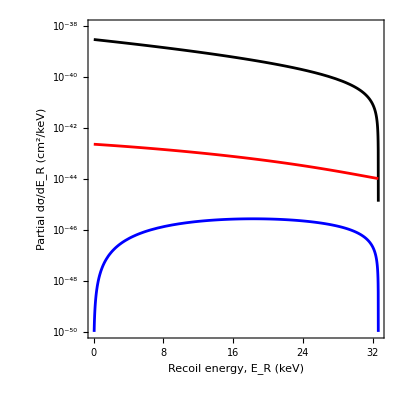

```mathematica
LogPlot[{dσMdEr[Er keV,45MeV,isotopesSN100PN["Cs133"],"νe"] Centimeter^-2 keV,dσΦdEr[Er keV,45MeV,isotopesSN100PN["Cs133"],"νe"] Centimeter^-2 keV,
dσAdEr[Er keV,45MeV,isotopesSN100PN["Cs133"],"νe"] Centimeter^-2 keV},{Er,.01,40},PlotRange->{10^-50,10^-38},
FrameLabel->{"Recoil energy, E_R (keV)","Partial  dσ/dE_R (cm^2/keV)"},PlotStyle->{{Black},{Blue},{Red}},
FrameTicks->{LogTicks[10^-50,10^-38,2],Automatic}]
```

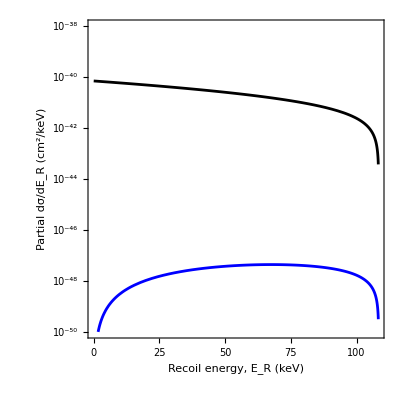

```mathematica
LogPlot[{dσMdEr[Er keV,45MeV,isotopesSDPFMU["Ar40"],"νe"] Centimeter^-2 keV,dσΦdEr[Er keV,45MeV,isotopesSDPFMU["Ar40"],"νe"] Centimeter^-2 keV,
dσAdEr[Er keV,45MeV,isotopesSDPFMU["Ar40"]] Centimeter^-2 keV},{Er,.01,TMAX[45MeV,0,40amu]/keV},PlotRange->{10^-50,10^-38},
FrameLabel->{"Recoil energy, E_R (keV)","Partial  dσ/dE_R (cm^2/keV)"},PlotStyle->{{Black},{Blue},{Red}},
FrameTicks->{LogTicks[10^-50,10^-38,2],Automatic}]
```

```mathematica
{σAvgCsIm,σAvgCsIϕ,σAvgCsIaxial}=ParallelTable[σAvg[targetCsI,cohSNSspectra,dσdE,"NA"]/Centimeter^2,{dσdE,{dσMdEr,dσΦdEr,dσAdEr}}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
σAvgCsIaxial=σAvg[targetCsI,cohSNSspectra,dσAdEr,"NA"]/Centimeter^2
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.63056×10^-42

```mathematica
{σAvgCsIm,σAvgCsIϕ,σAvgCsIaxial}
```

{1.86261×10^-38,2.59298×10^-45,1.63056×10^-42}

```mathematica
σAvvGeaxial=σAvg[targetGe,cohSNSspectra,dσAdEr,"NA"]/Centimeter^2
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

2.63482×10^-43

```mathematica
σAvgGeM=σAvg[targetGe,cohSNSspectra,dσMdEr,"NA"]/Centimeter^2
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

5.90408×10^-39

This result was used to justify discussion in paper about the negligible impact of the additional contributions to the cross section.

## COHERENT experimental runs

### CsI run II

These results were published in arXiv:

COHERENT prediction = 341 +± 11(theory)±41(exp)
experimental data         = 306±20

Details of analysis from arXiv:2110.07730v2

```mathematica
expResultCsI=Around[306,20];
coherentPredictionCsI=Around[341,√(11^2+41^2)];
```

#### Experimental parameters

Quenching response:

```mathematica
Eee[er_]:=(a er/MeV +b (er/MeV)^2+c (er/MeV)^3+d(er/MeV)^4)MeV/.{a->0.0554628,b-> 4.30681,c->-111.707,d-> 840.384}
```

Light yield converted to PE:

```mathematica
PE[Eee_]=13.35/keV Eee;
```

Source for sns efficiency (unitStep added by me to enforce ≥0):
https://arxiv.org/src/2110.07730v2/anc/effCoefficients.txt

```mathematica
snsCsIeff[pe_]=(a/(1+Exp[-b(pe-c)])+d)UnitStep[pe-7.0682]/.{a->1.32045,b-> 0.285979,c->10.8646,d->-0.333322};
```

Efficiency in time (this is now applied with ROOT macro and is not used):

```mathematica
snsCsIeffT[tμs_]=If[tμs<0.52,1,Exp[-0.0494(tμs-0.52)]];
```

Timing efficiency factors (obtained from root file and macro):

```mathematica
tEffCsIνe  = 0.8508;
tEffCsIνμ  = 0.9976;
tEffCsIνμb = 0.8512;
```

Energy resolution:

```mathematica
Pspe[pe_,Eee_]=(a(1+b))^(1+b)/Gamma[1+b] pe^b Exp[-a(1+b)pe]/.{a->0.0749/(Eee/keV),b->9.56 Eee/keV}//FullSimplify;
```

Total fluxes at detector after timing cuts:

```mathematica
With[{distance=19.3Meter,POT=3.198 10^23,νPerP=0.0848},
cohCsIFluxes={tEffCsIνe snsFlux[distance,POT,νPerP],tEffCsIνμ snsFlux[distance,POT,νPerP],tEffCsIνμb snsFlux[distance,POT,νPerP]};
]
```

#### Calculate total number of events

With coherent defined spectra:

```mathematica
With[{detMass=14.6 Kilogram},

{{diffRateCsIKN,diffRateCsIKNalt},{diffRateCsIFull,diffRateCsIFullAlt},{diffRateCsISHF,diffRateCsISHFAlt}}=Table[ParallelTable[{er,dRcevnsdE[er,target,cohSNSspectra,cohCsIFluxes,dσdE]},{er,logSpace[6keV,60keV,200]}]//Interpolation[#,InterpolationOrder->1]&,{dσdE,{dσIFdEr,dσFulldEr,dσWdEr}},{target,{targetCsI,targetCsIalt}}];

{KNtotRateCoherentCsI,KNaltTotRateCoherentCsI,fullTotRateCoherentCsI,fullAltTotRateCoherentCsI,SHFTotRateCoherentCsI,SHFAltTotRateCoherentCsI}= ParallelTable[detMass NIntegrate[snsCsIeff[PEdet]Pspe[PEdet,Eee[er]]rate[er],{PEdet,7,60},{er,6keV,60keV},PrecisionGoal->3],{rate,{diffRateCsIKN,diffRateCsIKNalt,diffRateCsIFull,diffRateCsIFullAlt,diffRateCsISHF,diffRateCsISHFAlt}}];

]//AbsoluteTiming
```

{371.568,Null}

```mathematica
ChargePredictionCsI=Around[(KNtotRateCoherentCsI+KNaltTotRateCoherentCsI)/2,√(((KNtotRateCoherentCsI-KNaltTotRateCoherentCsI)/2)^2+(fracSysErrorCsI(KNtotRateCoherentCsI+KNaltTotRateCoherentCsI)/2)^2)];
SHFPredictionCsI=Around[(SHFTotRateCoherentCsI+SHFAltTotRateCoherentCsI)/2,√(((SHFTotRateCoherentCsI-SHFAltTotRateCoherentCsI)/2)^2+(fracSysErrorCsI(SHFTotRateCoherentCsI+SHFAltTotRateCoherentCsI)/2)^2)];
FullPredictionCsI=Around[(fullTotRateCoherentCsI+fullAltTotRateCoherentCsI)/2,√(((fullTotRateCoherentCsI-fullAltTotRateCoherentCsI)/2)^2+(fracSysErrorCsI(fullTotRateCoherentCsI+fullAltTotRateCoherentCsI)/2)^2)];
```

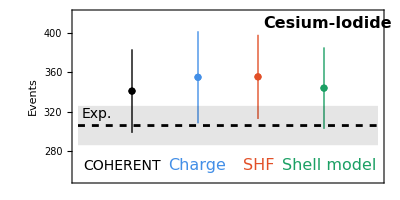

```mathematica
CsIeventsPlot=Show[ListPlot[{{0.9,coherentPredictionCsI}},PlotStyle->{Black,Thick,10},
AspectRatio->.5,FrameLabel->{None,"Events"},PlotRange->{{0,5},{251,420}},FrameTicks->{None,Automatic},ImageSize->400,
Prolog->{
Inset[Style["COHERENT",14,Black],Scaled[{.16,.1}]],
Inset[Style["Charge",16,MyBlue],Scaled[{.4,.1}]],
Inset[Style["SHF",16,MyRed],Scaled[{.6,.1}]],
Inset[Style["Shell model",16,MyGreen],Scaled[{.825,.1}]],
Inset[Style["Exp.",Italic,14,Black],Scaled[{.08,.4}]],
Inset[Style["Cesium-Iodide",16,Black,Bold,FontFamily->"Times"],Scaled[{.82,.92}]]}],
ListPlot[{{2,ChargePredictionCsI}},PlotStyle->{MyBlue,Thick}],
ListPlot[{{3,SHFPredictionCsI}},PlotStyle->{MyRed,Thick}],
ListPlot[{{4.1,FullPredictionCsI}},PlotStyle->{MyGreen,Thick}],
Plot[{expResultCsI["Value"]-expResultCsI["Uncertainty"],expResultCsI["Value"]+expResultCsI["Uncertainty"],expResultCsI["Value"]},{x,0,5},Filling->{1->{2}},FillingStyle->{Opacity[.1,Black]},PlotStyle->{None,None,{Black,Dashed}}]]
```

```mathematica
Export["figures/fig_CsI_events.pdf",CsIeventsPlot]
```

figures/fig_CsI_events.pdf

### LAr run I

#### Experimental parameters

Details taken from 2003.10630

```mathematica
expResultAr=Around[159,43];
cohPredictionAr=Around[128,17];
```

Efficiency curve:

```mathematica
coherentLArEffDat=Import["./data/COHERENT_Ar_I/CENNS10AnlAEfficiency.txt","Table"][[All,{1,3}]];
coherentLArEffDat[[All,1]]*=keV;
coherentLArEff=coherentLArEffDat//Interpolation[#,InterpolationOrder->1]&;
```

Quenching:

```mathematica
ArQF[ErNR_]:=0.246+0.00078*ErNR keV
EeAr[Er_]:=Er*ArQF[Er]
```

Energy resolution (denominator factor renormalises distribution near Ee->0):

```mathematica
sigmaEe[Ee_]:=0.58 √(Ee/keV)keV
EsmearAr[EE_,Ee_]=PDF[NormalDistribution[Ee,sigmaEe[Ee]],EE]/((1+Erf[Ee/(√2 sigmaEe[Ee])])/2);
```

```mathematica
tEffArνe  = 0.8658;
tEffArνμ  = 0.9999;
tEffArνμb = 0.8662;
```

Total flux:

```mathematica
With[{distance=27.5Meter,POT=13.8 10^22,νPerP=.09},
cohArFluxes={tEffArνe snsFlux[distance,POT,νPerP],tEffArνμ snsFlux[distance,POT,νPerP],tEffArνμb snsFlux[distance,POT,νPerP]};
]
```

#### Total events

```mathematica
With[{detMass=24.4 Kilogram,distance=27.5Meter,POT=13.8 10^22,νPerP=.09},

{{stdDiffRateCoherentAr,stdDiffRateCoherentArAlt},{fullDiffRateCoherentAr,fullDiffRateCoherentArAlt},{SHFdiffRateCoherentAr,SHFdiffRateCoherentArAlt}}= Table[ParallelTable[{er,detMass dRcevnsdE[er,target,cohSNSspectra,cohArFluxes,dσdE]},{er,logSpace[.01keV,240keV,200]}]//Interpolation[#,InterpolationOrder->1]&,{dσdE,{dσIFdEr,dσFulldEr,dσWdEr}},{target,{targetAr,targetArAlt}}];
 
{stdTotRateCoherentAr,stdTotRateCoherentArAlt,fullTotRateCoherentAr,fullTotRateCoherentArAlt,SHFTotRateCoherentAr,SHFTotRateCoherentArAlt}= ParallelTable[ NIntegrate[coherentLArEff[EeReco]EsmearAr[EeReco,EeAr[er]]rate[er],{er,.01keV,240keV},{EeReco,0.5keV,60keV},PrecisionGoal->3],{rate,{stdDiffRateCoherentAr,stdDiffRateCoherentArAlt,fullDiffRateCoherentAr,fullDiffRateCoherentArAlt,SHFdiffRateCoherentAr,SHFdiffRateCoherentArAlt}}];
 
]//AbsoluteTiming
```

{173.636,Null}

This compares with:
  COHERENT prediction = 128 +± 17
  experimental data         = 159 ± 43

The COHERENT error prediction error is made up several components listed in Table I of 2004.10630:

```mathematica
128 √((.036)^2+(.008)^2+(.078)^2+(.01)^2+(.02)^2+(.10)^2)
```

17.1463

We’ll remove the nuclear form factor component and assume the rest affect our result approximately the same:

```mathematica
fracSysError=√((.036)^2+(.008)^2+(.078)^2+(.01)^2+(.10)^2)
```

0.132454

Include 10% uncertainty from neutrino flux (said to be the dominant source)

```mathematica
ChargePredictionAr=Around[(stdTotRateCoherentAr+stdTotRateCoherentArAlt)/2,√(((stdTotRateCoherentAr-stdTotRateCoherentArAlt)/2)^2+(fracSysError (stdTotRateCoherentAr+stdTotRateCoherentArAlt)/2)^2)];
SHFPredictionAr=Around[(fullTotRateCoherentAr+fullTotRateCoherentArAlt)/2,√(((fullTotRateCoherentAr-fullTotRateCoherentArAlt)/2)^2+(fracSysError (fullTotRateCoherentAr+fullTotRateCoherentArAlt)/2)^2)];
FullPredictionCsI=Around[(fullTotRateCoherentAr+fullTotRateCoherentArAlt)/2,√(((fullTotRateCoherentAr-fullTotRateCoherentArAlt)/2)^2+(fracSysError (fullTotRateCoherentAr+fullTotRateCoherentArAlt)/2)^2)];
```

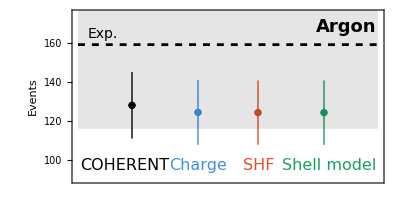

```mathematica
AreventsPlot=Show[ListPlot[{{0.9,cohPredictionAr}},PlotStyle->{Black,Thick,10},
AspectRatio->.5,FrameLabel->{"","Events"},PlotRange->{{0,5},{90,175}},FrameTicks->{None,Automatic},ImageSize->400,
Prolog->{
Inset[Style["Charge",16,MyBlue],Scaled[{.405,.1}]],
Inset[Style["SHF",16,MyRed],Scaled[{.6,.1}]],
Inset[Style["Shell model",16,MyGreen],Scaled[{.825,.1}]],
Inset[Style["COHERENT",16,Black],Scaled[{.17,.1}]],
Inset[Style["Exp.",Italic,14,Black],Scaled[{.1,.86}]],
Inset[Style["Argon",18,Black,Bold,FontFamily->"Times"],Scaled[{.88,.9}]]}],
ListPlot[{{2,ChargePredictionAr}},PlotStyle->{MyBlue,Thick}],
ListPlot[{{3,SHFPredictionAr}},PlotStyle->{MyRed,Thick}],
ListPlot[{{4.1,FullPredictionCsI}},PlotStyle->{MyGreen,Thick}],
Plot[{159-43,159+43,159},{x,0,5},Filling->{1->{2}},FillingStyle->{Opacity[.1,Black]},PlotStyle->{None,None,{Black,Dashed}}]]
```

```mathematica
Export["figures/fig_Ar_events.pdf",AreventsPlot];
```